# Método de los momentos aproximados - Chi cuadrado

```mathematica
(*Muestra de la distribución chi cuadrado*)
```

```mathematica
SeedRandom[4321]
```

```mathematica
datos1 = RandomVariate[ChiSquareDistribution[5],10^4]
```

{3.92611,2.34812,4.86475,5.40946,9.92656,2.7506,5.57054,2.11573,2.97587,3.94655,2.96345,3.44625,6.41102,5.97522,1.41236,9970,5.86054,2.81497,2.71407,1.63191,1.32977,2.69402,3.82371,2.31427,4.14147,5.97406,3.2106,6.68792,2.10678,2.86916,1.42768}
 |  |  |  |

```mathematica
Export["DatosChi.xlsx",datos1]
```

DatosChi.xlsx

```mathematica
Select[datos1,#>25&]
```

{}

### MOP DE GRADO 3

```mathematica
(*Momentos poblacionales*)
```

```mathematica
Integrate[x*(b*x+c*x^2+d*x^3),{x,0,25}]
```

(15625 b)/3+(390625 c)/4+1953125 d

```mathematica
Integrate[x^2*(b*x+c*x^2+d*x^3),{x,0,25}]
```

(390625 b)/4+1953125 c+(244140625 d)/6

```mathematica
Integrate[x^3*(b*x+c*x^2+d*x^3),{x,0,25}]
```

1953125 b+(244140625 c)/6+(6103515625 d)/7

```mathematica
F3[b_,c_,d_]= ((15625 b)/3+(390625 c)/4+1953125 d-(Apply[Plus,datos1])/10^4)^2+((390625 b)/4+1953125 c+(244140625 d)/6-(Apply[Plus,datos1^2])/10^4)^2+(1953125 b+(244140625 c)/6+(6103515625 d)/7-(Apply[Plus,datos1^3])/10^4)^2
```

(-5.01025+(15625 b)/3+(390625 c)/4+1953125 d)^2+(-35.3233+(390625 b)/4+1953125 c+(244140625 d)/6)^2+(-320.775+1953125 b+(244140625 c)/6+(6103515625 d)/7)^2

```mathematica
Minimize[{F3[b,c,d],{25b+(25^2)c+(25^3)d>0}},{b,c,d}]
```

{0.000590764,{b→0.0359755,c→-0.00394197,d→0.000103741}}

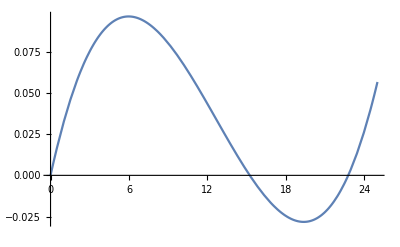

```mathematica
Plot[b*x+c*x^2+d*x^3/.{b->0.035975528392871214,c->-0.0039419735760078,d->0.00010374147351813457},{x,0,25}]
```

```mathematica
F31[x_]=b*x+c*x^2+d*x^3/.{b->0.035975528392871214,c->-0.0039419735760078,d->0.00010374147351813457}
```

0.0359755 x-0.00394197 x^2+0.000103741 x^3

```mathematica
Solve[F31[x]==0,Reals]
```

{{x→0},{x→15.2331},{x→22.765}}

```mathematica
APN =- Integrate[F31[x],{x,15.23307854315858,22.764970282692364}]
```

0.14036

```mathematica
AT = Integrate[F31[x],{x,0,15.23307854315858}]- Integrate[F31[x],{x,15.23307854315858,22.764970282692364}]+Integrate[F31[x],{x,22.764970282692364,25}]
```

1.12296

```mathematica
APN/AT
```

0.124991

```mathematica
(*Como el área de la parte negativa es mayor del 1% del área total, seguimos añadiendo restricciones*)
```

```mathematica
f[x_]=b*x+c*x^2+d*x^3
```

b x+c x^2+d x^3

```mathematica
f[(15.23307854315858+22.764970282692364)/2]
```

18.999 b+360.963 c+6857.94 d

```mathematica
Minimize[{F3[b,c,d],{25b+(25^2)c+(25^3)d>0,18.999024412925472 b+360.9629286429381 c+6857.943493448256 d>0}},{b,c,d}]
```

{1.05693×10^6,{b→-0.614949,c→0.055473,d→-0.00121074}}

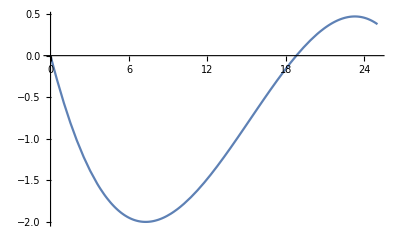

```mathematica
Plot[b*x+c*x^2+d*x^3/.{b->-0.6149494587170308,c->0.05547295687230657,d->-0.0012107390711216146}, {x,0,25}]
```

```mathematica
(*Como el área de la parte negativa es superior al 1% del área total, seguimos añadiendo restricciones*)
```

```mathematica
F32[x_]=b*x+c*x^2+d*x^3/.{b->-0.6149494587170308,c->0.05547295687230657,d->-0.0012107390711216146}
```

-0.614949 x+0.055473 x^2-0.00121074 x^3

```mathematica
Solve[F32[x]==0,Reals]
```

{{x→0},{x→18.7981},{x→27.0193}}

```mathematica
(*Como el área de la parte negativa es mayor del 1% del área total, seguimos añadiendo restricciones*)
```

```mathematica
f[(18.79813964391716)/2]
```

9.39907 b+88.3425 c+830.337 d

```mathematica
Minimize[{F3[b,c,d],{25b+(25^2)c+(25^3)d>0,18.999024412925472 b+360.9629286429381 c+6857.943493448256 d>0,
9.39906982195858 b+88.3425135180525 c+830.3374528034951 d>0}},{b,c,d}]
```

{218.455,{b→0.00361662,c→-0.000322799,d→7.33316×10^-6}}

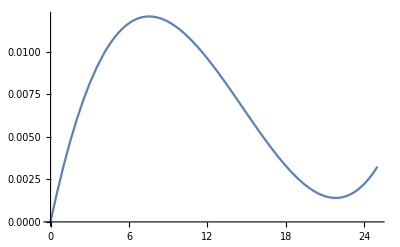

```mathematica
Plot[b*x+c*x^2+d*x^3/.{b->0.003616620433264152,c->-0.0003227990029560025,d->7.3331614965434915*^-6},{x,0,25}]
```

```mathematica
(*Como ya no hay parte negativa, dejamos de añadir restricciones)
```

```mathematica
(*Obtención de la densidad y representación gráfica*)
```

```mathematica
Integrate[b*x+c*x^2+d*x^3/.{b->0.003616620433264152,c->-0.0003227990029560025,d->7.3331614965434915*^-6},{x,0,25}]
```

0.165078

```mathematica
f3[x_]=(b*x+c*x^2+d*x^3)/0.16507813072936006/.{b->0.003616620433264152,c->-0.0003227990029560025,d->7.3331614965434915*^-6}
```

6.05774 (0.00361662 x-0.000322799 x^2+7.33316×10^-6 x^3)

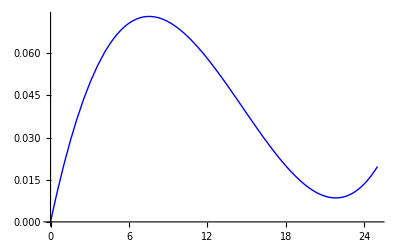

```mathematica
Plot[f3[x],{x,0,25},PlotStyle->{Blue,Thin}]
```

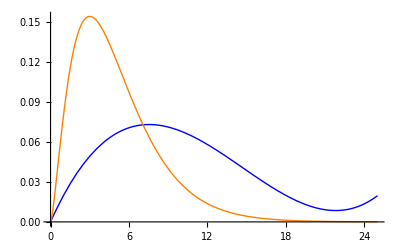

```mathematica
Plot[{f3[x],PDF[ChiSquareDistribution[5],x]},{x,0,25},PlotStyle->{{Blue,Thin},{Orange,Thin}}]
```

```mathematica
(*Divergencia de Kullback-Leibler*)
N[Integrate[PDF[ChiSquareDistribution[5],x],{x,0,25}]]
```

0.999861

```mathematica
G[x_]=(PDF[ChiSquareDistribution[5],x])/0.9998606662088144
```

1.00014 (Piecewise[{{(ⅇ^(-x/2) x^(3/2))/(3 √(2 π)), x>0}, {0, True}}])

```mathematica
KL3=N[Integrate[G[x]*Log[G[x]/f3[x]],{x,0,25}]]
```

0.544578

```mathematica
(*Verosimilitud*)
```

```mathematica
x3 = Log[f3[datos1]]
```

{-2.83767,-3.18841,-2.72697,-2.68348,-2.68464,-3.07064,-2.67304,-3.26964,-3.0149,-2.83468,-3.01781,-2.91698,-2.634,-2.65115,9972,-3.05404,-3.0803,-3.48225,-3.65816,-3.08569,-2.8531,-3.19957,-2.8076,-2.65121,-2.9632,-2.62627,-3.273,-3.0405,-3.59641}
 |  |  |  |

```mathematica
V3 = Apply[Plus,x3]
```

-29693.6

```mathematica
(*BIC*)
```

```mathematica
B3 = -2*V3 + 3*Log[10000]
```

59414.8

### MOP DE GRADO 4

```mathematica
(*Momentos poblacionales*)
```

```mathematica
Integrate[x*(b*x+c*x^2+d*x^3+e*x^4),{x,0,25}]
```

(15625 b)/3+(390625 c)/4+1953125 d+(244140625 e)/6

```mathematica
Integrate[x^2*(b*x+c*x^2+d*x^3+e*x^4),{x,0,25}]
```

(390625 b)/4+1953125 c+(244140625 d)/6+(6103515625 e)/7

```mathematica
Integrate[x^3*(b*x+c*x^2+d*x^3+e*x^4),{x,0,25}]
```

1953125 b+(244140625 c)/6+(6103515625 d)/7+(152587890625 e)/8

```mathematica
Integrate[x^4*(b*x+c*x^2+d*x^3+e*x^4),{x,0,25}]
```

(244140625 b)/6+(6103515625 c)/7+(152587890625 d)/8+(3814697265625 e)/9

```mathematica
F4[b_,c_,d_,e_]=((15625 b)/3+(390625 c)/4+1953125 d+(244140625 e)/6-(Apply[Plus,datos1])/10^4)^2+((390625 b)/4+1953125 c+(244140625 d)/6+(6103515625 e)/7-(Apply[Plus,datos1^2])/10^4)^2+(1953125 b+(244140625 c)/6+(6103515625 d)/7+(152587890625 e)/8-(Apply[Plus,datos1^3])/10^4)^2+((244140625 b)/6+(6103515625 c)/7+(152587890625 d)/8+(3814697265625 e)/9-(Apply[Plus,datos1^4])/10^4)^2
```

(-5.01025+(15625 b)/3+(390625 c)/4+1953125 d+(244140625 e)/6)^2+(-35.3233+(390625 b)/4+1953125 c+(244140625 d)/6+(6103515625 e)/7)^2+(-320.775+1953125 b+(244140625 c)/6+(6103515625 d)/7+(152587890625 e)/8)^2+(-3541.44+(244140625 b)/6+(6103515625 c)/7+(152587890625 d)/8+(3814697265625 e)/9)^2

```mathematica
Minimize[{F4[b,c,d,e],{25b+25^2c+25^3d+25^4e>0}},{b,c,d,e}]
```

{3.65162×10^6,{b→-149.567,c→31.5289,d→-2.02295,e→0.0405318}}

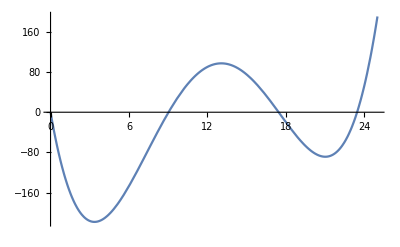

```mathematica
Plot[b*x+c*x^2+d*x^3+e*x^4/.{b->-149.56700010494265,c->31.5288569410299,d->-2.0229489350528236,e->0.040531779594962625},{x,0,25}]
```

```mathematica
(*Como el área de la parte negativa es superior al 1% del total, seguimos añadiendo restricciones*)
```

```mathematica
F41[x_]=b*x+c*x^2+d*x^3+e*x^4/.{b->-149.56700010494265,c->31.5288569410299,d->-2.0229489350528236,e->0.040531779594962625}
```

-149.567 x+31.5289 x^2-2.02295 x^3+0.0405318 x^4

```mathematica
Solve[F41[x]==0,Reals]
```

{{x→0},{x→9.02397},{x→17.4436},{x→23.4426}}

```mathematica
f[x_]=b*x+c*x^2+d*x^3+e*x^4
```

b x+c x^2+d x^3+e x^4

```mathematica
f[9.02397122115271/2]
```

4.51199 b+20.358 c+91.8551 d+414.449 e

```mathematica
f[(17.4436176233647+23.442603978702213)/2]
```

20.4431 b+417.921 c+8543.6 d+174658. e

```mathematica
Minimize[{F4[b,c,d,e],{25b+25^2c+25^3d+25^4e>0,
4.511985610576355 b+20.35801415004808 c+91.85506690492677 d+414.4487401335579 e>0,
20.443110801033455 b+417.9207792233307 c+8543.600795716791 d+174657.77770663594 e>0}},{b,c,d,e}]
```

{3.34914×10^11,{b→31.6554,c→-7.96513,d→0.523812,e→-0.0102249}}

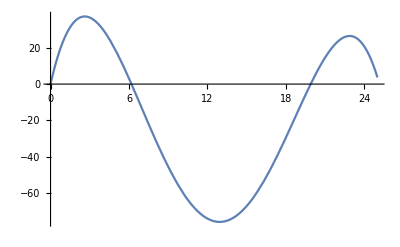

```mathematica
Plot[b*x+c*x^2+d*x^3+e*x^4/.{b->31.655374175747028,c->-7.965126584419173,d->0.5238123117851009,e->-0.01022493045820204},{x,0,25}]
```

```mathematica
F42[x_]=b*x+c*x^2+d*x^3+e*x^4/.{b->31.655374175747028,c->-7.965126584419173,d->0.5238123117851009,e->-0.01022493045820204}
```

31.6554 x-7.96513 x^2+0.523812 x^3-0.0102249 x^4

```mathematica
Solve[F42[x]==0,Reals]
```

{{x→0},{x→6.18871},{x→19.8923},{x→25.148}}

```mathematica
(*Como el área de la parte negativa es superior al 1% del área total, seguimos añadiendo restricciones*)
```

```mathematica
f[(6.188708893796233+19.89226367467132)/2]
```

13.0405 b+170.054 c+2217.59 d+28918.5 e

```mathematica
Minimize[{F4[b,c,d,e],{25b+25^2c+25^3d+25^4e>0,
4.511985610576355 b+20.35801415004808 c+91.85506690492677 d+414.4487401335579 e>0,
20.443110801033455 b+417.9207792233307 c+8543.600795716791 d+174657.77770663594 e>0,
13.040486284233776 b+170.05428252928922 c+2217.5905388984115 d+28918.459006551322 e>0}},{b,c,d,e}]
```

{5.99067×10^11,{b→0.0741705,c→0.0000610416,d→-0.000186057,e→2.95846×10^-6}}

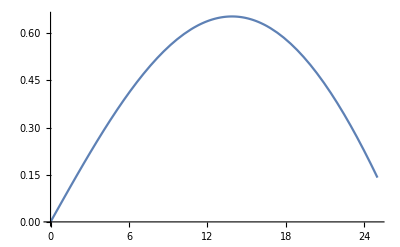

```mathematica
Plot[b*x+c*x^2+d*x^3+e*x^4/.{b->0.07417048359070455,c->0.0000610416293047244,d->-0.00018605704579318717,e->2.9584646248341014*^-6},{x,0,25}]
```

```mathematica
(*Como ya no hay parte negativa, dejamos de añadir restricciones*)
```

```mathematica
(*Obtención de la densidad y representación*)
```

```mathematica
Integrate[b*x+c*x^2+d*x^3+e*x^4/.{b->0.07417048359070455,c->0.0000610416293047244,d->-0.00018605704579318717,e->2.9584646248341014*^-6},{x,0,25}]
```

11.1048

```mathematica
f4[x_]=(b*x+c*x^2+d*x^3+e*x^4)/11.104819116862117/.{b->0.07417048359070455,c->0.0000610416293047244,d->-0.00018605704579318717,e->2.9584646248341014*^-6}
```

0.090051 (0.0741705 x+0.0000610416 x^2-0.000186057 x^3+2.95846×10^-6 x^4)

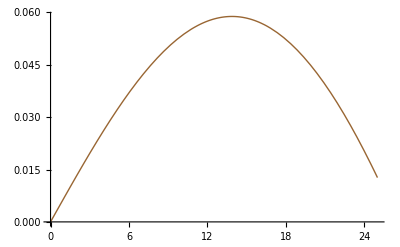

```mathematica
Plot[f4[x],{x,0,25},PlotStyle->{Brown,Thin}]
```

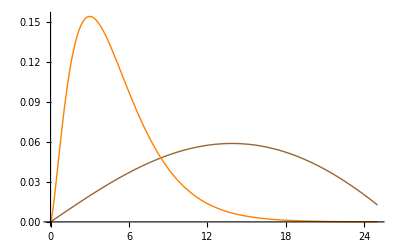

```mathematica
Plot[{f4[x],PDF[ChiSquareDistribution[5],x]},{x,0,25},PlotStyle->{{Brown,Thin},{Orange,Thin}}]
```

```mathematica
(*Divergencia de Kullback-Leibler*)
N[Integrate[PDF[ChiSquareDistribution[5],x],{x,0,25}]]
```

0.999861

```mathematica
G[x_]=(PDF[ChiSquareDistribution[5],x])/0.9998606662088144
```

1.00014 (Piecewise[{{(ⅇ^(-x/2) x^(3/2))/(3 √(2 π)), x>0}, {0, True}}])

```mathematica
KL4=N[Integrate[G[x]*Log[G[x]/f4[x]],{x,0,25}]]
```

1.27027

```mathematica
(*Verosimilitud*)
```

```mathematica
x4 = Log[f4[datos1]]
```

{-3.6747,-4.1666,-3.47886,-3.38531,-2.93669,-4.01296,-3.35994,-4.26852,-3.93712,-3.66987,-3.94114,-3.79713,-3.24212,-3.30034,-4.66725,9971,-3.99063,-4.02589,-4.5242,-4.72701,-4.03306,-3.69935,-4.18077,-3.62519,-3.3005,-3.86445,-3.20803,-4.27268,-3.97225,-4.65655}
 |  |  |  |

```mathematica
V4 = Apply[Plus,x4]
```

-36930.2

```mathematica
(*BIC*)
```

```mathematica
B4 = -2*V4 + 4*Log[10000]
```

73897.3

### MOP DE GRADO 5

```mathematica
(*Momentos poblacionales*)
```

```mathematica
Integrate[x*(b*x+c*x^2+d*x^3+e*x^4+f*x^5),{x,0,25}]
```

(15625 b)/3+(390625 c)/4+1953125 d+(244140625 e)/6+(6103515625 f)/7

```mathematica
Integrate[x^2*(b*x+c*x^2+d*x^3+e*x^4+f*x^5),{x,0,25}]
```

(390625 b)/4+1953125 c+(244140625 d)/6+(6103515625 e)/7+(152587890625 f)/8

```mathematica
Integrate[x^3*(b*x+c*x^2+d*x^3+e*x^4+f*x^5),{x,0,25}]
```

1953125 b+(244140625 c)/6+(6103515625 d)/7+(152587890625 e)/8+(3814697265625 f)/9

```mathematica
Integrate[x^4*(b*x+c*x^2+d*x^3+e*x^4+f*x^5),{x,0,25}]
```

(244140625 b)/6+(6103515625 c)/7+(152587890625 d)/8+(3814697265625 e)/9+(19073486328125 f)/2

```mathematica
Integrate[x^5*(b*x+c*x^2+d*x^3+e*x^4+f*x^5),{x,0,25}]
```

(6103515625 b)/7+(152587890625 c)/8+(3814697265625 d)/9+(19073486328125 e)/2+(2384185791015625 f)/11

```mathematica
F5[b_,c_,d_,e_,f_]=((15625 b)/3+(390625 c)/4+1953125 d+(244140625 e)/6+(6103515625 f)/7-(Apply[Plus,datos1])/10^4)^2+((390625 b)/4+1953125 c+(244140625 d)/6+(6103515625 e)/7+(152587890625 f)/8-(Apply[Plus,datos1^2])/10^4)^2+(1953125 b+(244140625 c)/6+(6103515625 d)/7+(152587890625 e)/8+(3814697265625 f)/9-(Apply[Plus,datos1^3])/10^4)^2*((244140625 b)/6+(6103515625 c)/7+(152587890625 d)/8+(3814697265625 e)/9+(19073486328125 f)/2-(Apply[Plus,datos1^4])/10^4)^2+((6103515625 b)/7+(152587890625 c)/8+(3814697265625 d)/9+(19073486328125 e)/2+(2384185791015625 f)/11-(Apply[Plus,datos1^5])/10^4)^2
```

(-5.01025+(15625 b)/3+(390625 c)/4+1953125 d+(244140625 e)/6+(6103515625 f)/7)^2+(-35.3233+(390625 b)/4+1953125 c+(244140625 d)/6+(6103515625 e)/7+(152587890625 f)/8)^2+(-320.775+1953125 b+(244140625 c)/6+(6103515625 d)/7+(152587890625 e)/8+(3814697265625 f)/9)^2 (-3541.44+(244140625 b)/6+(6103515625 c)/7+(152587890625 d)/8+(3814697265625 e)/9+(19073486328125 f)/2)^2+(-45551.3+(6103515625 b)/7+(152587890625 c)/8+(3814697265625 d)/9+(19073486328125 e)/2+(2384185791015625 f)/11)^2

```mathematica
Minimize[F5[b,c,d,e,f],{25 b+625 c+15625 d+390625 e+9765625 f>0},{b,c,d,e,f}]
```

{6.03679×10^11,{b→-8276.77,c→1477.93,d→-75.3304,e→0.672277,f→0.0209711}}

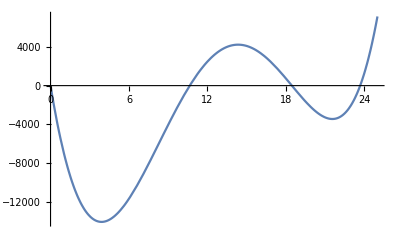

```mathematica
Plot[b*x+c*x^2+d*x^3+e*x^4+f*x^5/.{b->-8276.766016454218,c->1477.927695732234,d->-75.3303524974245,e->0.6722767324148939,f->0.02097112337769199},{x,0,25}]
```

```mathematica
(*Como el área de la parte negativa es superior al 1% del área total, seguimos añadiendo restricciones*)
```

```mathematica
F51[x_]=b*x+c*x^2+d*x^3+e*x^4+f*x^5/.{b->-8276.766016454218,c->1477.927695732234,d->-75.3303524974245,e->0.6722767324148939,f->0.02097112337769199}
```

-8276.77 x+1477.93 x^2-75.3304 x^3+0.672277 x^4+0.0209711 x^5

```mathematica
Solve[F51[x]==0,Reals]
```

{{x→-84.8368},{x→0},{x→10.6457},{x→18.4562},{x→23.6776}}

```mathematica
(*Como el área de la parte negativa es superior al 1% del área total, seguimos añadiendo restricciones*)
```

```mathematica
f[x_]=b*x+c*x^2+d*x^3+e*x^4+f*x^5
```

b x+c x^2+d x^3+e x^4+f x^5

```mathematica
f[(10.645728251400254)/2]
```

5.32286 b+28.3329 c+150.812 d+802.752 e+4272.94 f

```mathematica
f[(18.456213338492624+23.67755925305783)/2]
```

21.0669 b+443.814 c+9349.77 d+196971. e+4.14956×10^6 f

```mathematica
Minimize[F5[b,c,d,e,f],{25 b+625 c+15625 d+390625 e+9765625 f>0,
5.322864125700127 b+28.332882500665374 c+150.8120838404686 d+802.7522307965102 e+4272.941051132492 f>0,
21.066886295775227 b+443.81369819912203 c+9349.772716468406 d+196970.59870918136 e+4.149557206617094*^6 f>0},{b,c,d,e,f}]
```

{7.41×10^27,{b→127961.,c→-43688.6,d→4729.8,e→-205.619,f→3.12743}}

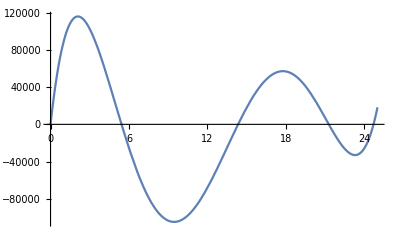

```mathematica
Plot[b*x+c*x^2+d*x^3+e*x^4+f*x^5/.{b->127961.43973096747,c->-43688.57747321567,d->4729.802921727861,e->-205.6187998613766,f->3.1274274760102228},{x,0,25}]
```

```mathematica
(*Como el área de la parte negativa es superior al 1% del área total, seguimos añadiendo restricciones*)
```

```mathematica
F52[x_]=b*x+c*x^2+d*x^3+e*x^4+f*x^5/.{b->127961.43973096747,c->-43688.57747321567,d->4729.802921727861,e->-205.6187998613766,f->3.1274274760102228}
```

127961. x-43688.6 x^2+4729.8 x^3-205.619 x^4+3.12743 x^5

```mathematica
Solve[F52[x]==0,Reals]
```

{{x→0},{x→5.4287},{x→14.3411},{x→21.2784},{x→24.6987}}

```mathematica
f[(5.428695772840521+14.34109864534799)/2]
```

9.8849 b+97.7112 c+965.865 d+9547.48 e+94375.8 f

```mathematica
f[(21.27840122177617+24.698748594116317)/2]
```

22.9886 b+528.475 c+12148.9 d+279285. e+6.42037×10^6 f

```mathematica
Minimize[F5[b,c,d,e,f],{25 b+625 c+15625 d+390625 e+9765625 f>0,
5.322864125700127 b+28.332882500665374 c+150.8120838404686 d+802.7522307965102 e+4272.941051132492 f>0,
21.066886295775227 b+443.81369819912203 c+9349.772716468406 d+196970.59870918136 e+4.149557206617094*^6 f>0,
9.884897209094255 b+97.7111928343594 c+965.8650973456298 d+9547.477205113366 e+94375.83077871613 f>0,
22.988574907946244 b+528.4745762982557 c+12148.877384177604 d+279285.37779362086 e+6.42037282810272*^6 f>0},{b,c,d,e,f}]
```

{1.12856×10^23,{b→-38864.9,c→14556.8,d→-1765.22,e→84.0607,f→-1.36979}}

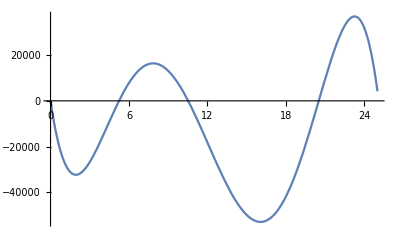

```mathematica
Plot[b*x+c*x^2+d*x^3+e*x^4+f*x^5/.{b->-38864.89460761606,c->14556.80213749444,d->-1765.2165633882921,e->84.06074409464472,f->-1.369794409665306},{x,0,25}]
```

```mathematica
(*Como el área de la parte negativa es superior al 1% del área total, seguimos añadiendo restricciones*)
```

```mathematica
F53[x_]=b*x+c*x^2+d*x^3+e*x^4+f*x^5/.{b->-38864.89460761606,c->14556.80213749444,d->-1765.2165633882921,e->84.06074409464472,f->-1.369794409665306}
```

-38864.9 x+14556.8 x^2-1765.22 x^3+84.0607 x^4-1.36979 x^5

```mathematica
Solve[F53[x]==0,Reals]
```

{{x→0},{x→5.23731},{x→10.5259},{x→20.5087},{x→25.0955}}

```mathematica
f[(5.237312172253816)/2]
```

2.61866 b+6.85736 c+17.9571 d+47.0234 e+123.138 f

```mathematica
f[(10.52590879151365+20.50873435377975)/2]
```

15.5173 b+240.787 c+3736.37 d+57978.5 e+899671. f

```mathematica
Minimize[F5[b,c,d,e,f],{25 b+625 c+15625 d+390625 e+9765625 f>0,
5.322864125700127 b+28.332882500665374 c+150.8120838404686 d+802.7522307965102 e+4272.941051132492 f>0,
21.066886295775227 b+443.81369819912203 c+9349.772716468406 d+196970.59870918136 e+4.149557206617094*^6 f>0,
9.884897209094255 b+97.7111928343594 c+965.8650973456298 d+9547.477205113366 e+94375.83077871613 f>0,
22.988574907946244 b+528.4745762982557 c+12148.877384177604 d+279285.37779362086 e+6.42037282810272*^6 f>0,
2.618656086126908 b+6.857359697409496 c+17.957066706382747 d+47.023382019656054 e+123.13806551604294 f>0,
15.5173215726467 b+240.78726878892667 c+3736.3734803970915 d+57978.50881083082 e+899671.1655201919 f>0},{b,c,d,e,f}]
```

{9.3345×10^22,{b→15.674,c→-3.35265,d→0.26736,e→-0.00937607,f→0.000121879}}

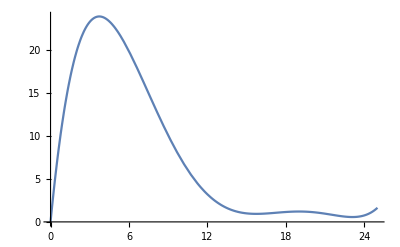

```mathematica
Plot[b*x+c*x^2+d*x^3+e*x^4+f*x^5/.{b->15.674031476913349,c->-3.3526506469653095,d->0.26736044409104853,e->-0.009376068280699751,f->0.00012187852788088237},{x,0,25}]
```

```mathematica
(*Como ya no hay parte negativa, dejamos de añadir restricciones*)
```

```mathematica
(*Obtención de la densidad y representación gráfica*)
```

```mathematica
Integrate[b*x+c*x^2+d*x^3+e*x^4+f*x^5/.{b->15.674031476913349,c->-3.3526506469653095,d->0.26736044409104853,e->-0.009376068280699751,f->0.00012187852788088237},{x,0,25}]
```

192.448

```mathematica
f5[x_]=(b*x+c*x^2+d*x^3+e*x^4+f*x^5)/192.44771960228536/.{b->15.674031476913349,c->-3.3526506469653095,d->0.26736044409104853,e->-0.009376068280699751,f->0.00012187852788088237}
```

0.00519622 (15.674 x-3.35265 x^2+0.26736 x^3-0.00937607 x^4+0.000121879 x^5)

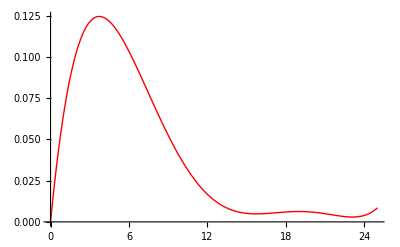

```mathematica
Plot[f5[x],{x,0,25},PlotStyle->{Red,Thin}]
```

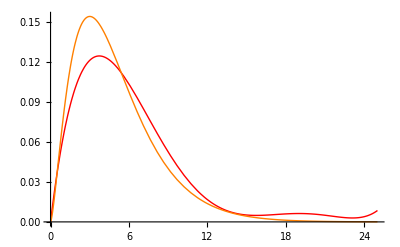

```mathematica
Plot[{f5[x],PDF[ChiSquareDistribution[5],x]},{x,0,25},PlotStyle->{{Red,Thin},{Orange,Thin}}]
```

```mathematica
(*Divergencia de Kullback-Leibler*)
```

```mathematica
KL5=N[Integrate[G[x]*Log[G[x]/f5[x]],{x,0,25}]]
```

0.0482224

```mathematica
(*Verosimilitud*)
```

```mathematica
x5 = Log[f5[datos1]]
```

{-2.08489,-2.19158,-2.13444,-2.18995,-3.2511,-2.13333,-2.2097,-2.23921,-2.11169,-2.08526,-2.11271,-2.08686,-2.33563,-2.26565,9972,-2.12642,-2.13752,-2.38361,-2.51806,-2.13991,-2.08357,-2.1978,-2.0905,-2.26547,-2.09614,-2.38518,-2.24129,-2.12107,-2.46966}
 |  |  |  |

```mathematica
V5 = Apply[Plus,x5]
```

-24766.

```mathematica
(*BIC*)
```

```mathematica
B5 = -2*V5 + 5*Log[10000]
```

49578.

### MOP DE GRADO 6

```mathematica
(*Momentos poblacionales*)
```

```mathematica
Integrate[x*(b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6),{x,0,25}]
```

(15625 b)/3+(390625 c)/4+1953125 d+(244140625 e)/6+(6103515625 f)/7+(152587890625 g)/8

```mathematica
Integrate[x^2*(b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6),{x,0,25}]
```

(390625 b)/4+1953125 c+(244140625 d)/6+(6103515625 e)/7+(152587890625 f)/8+(3814697265625 g)/9

```mathematica
Integrate[x^3*(b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6),{x,0,25}]
```

1953125 b+(244140625 c)/6+(6103515625 d)/7+(152587890625 e)/8+(3814697265625 f)/9+(19073486328125 g)/2

```mathematica
Integrate[x^4*(b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6),{x,0,25}]
```

(244140625 b)/6+(6103515625 c)/7+(152587890625 d)/8+(3814697265625 e)/9+(19073486328125 f)/2+(2384185791015625 g)/11

```mathematica
Integrate[x^5*(b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6),{x,0,25}]
```

(6103515625 b)/7+(152587890625 c)/8+(3814697265625 d)/9+(19073486328125 e)/2+(2384185791015625 f)/11+(59604644775390625 g)/12

```mathematica
Integrate[x^6*(b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6),{x,0,25}]
```

(152587890625 b)/8+(3814697265625 c)/9+(19073486328125 d)/2+(2384185791015625 e)/11+(59604644775390625 f)/12+(1490116119384765625 g)/13

```mathematica
F6[b_,c_,d_,e_,f_,g_]= ((15625 b)/3+(390625 c)/4+1953125 d+(244140625 e)/6+(6103515625 f)/7+(152587890625 g)/8-(Apply[Plus,datos1])/10^4)^2+((390625 b)/4+1953125 c+(244140625 d)/6+(6103515625 e)/7+(152587890625 f)/8+(3814697265625 g)/9-(Apply[Plus,datos1^2])/10^4)^2+(1953125 b+(244140625 c)/6+(6103515625 d)/7+(152587890625 e)/8+(3814697265625 f)/9+(19073486328125 g)/2-(Apply[Plus,datos1^3])/10^4)^2+((244140625 b)/6+(6103515625 c)/7+(152587890625 d)/8+(3814697265625 e)/9+(19073486328125 f)/2+(2384185791015625 g)/11-(Apply[Plus,datos1^4])/10^4)^2+((6103515625 b)/7+(152587890625 c)/8+(3814697265625 d)/9+(19073486328125 e)/2+(2384185791015625 f)/11+(59604644775390625 g)/12-(Apply[Plus,datos1^5])/10^4)^2+((152587890625 b)/8+(3814697265625 c)/9+(19073486328125 d)/2+(2384185791015625 e)/11+(59604644775390625 f)/12+(1490116119384765625 g)/13-(Apply[Plus,datos1^6])/10^4)^2
```

(-5.01025+(15625 b)/3+(390625 c)/4+1953125 d+(244140625 e)/6+(6103515625 f)/7+(152587890625 g)/8)^2+(-35.3233+(390625 b)/4+1953125 c+(244140625 d)/6+(6103515625 e)/7+(152587890625 f)/8+(3814697265625 g)/9)^2+(-320.775+1953125 b+(244140625 c)/6+(6103515625 d)/7+(152587890625 e)/8+(3814697265625 f)/9+(19073486328125 g)/2)^2+(-3541.44+(244140625 b)/6+(6103515625 c)/7+(152587890625 d)/8+(3814697265625 e)/9+(19073486328125 f)/2+(2384185791015625 g)/11)^2+(-45551.3+(6103515625 b)/7+(152587890625 c)/8+(3814697265625 d)/9+(19073486328125 e)/2+(2384185791015625 f)/11+(59604644775390625 g)/12)^2+(-660392.+(152587890625 b)/8+(3814697265625 c)/9+(19073486328125 d)/2+(2384185791015625 e)/11+(59604644775390625 f)/12+(1490116119384765625 g)/13)^2

```mathematica
Minimize[F6[b,c,d,e,f,g],{25 b+25^2c+25^3d+25^4 e+25^5f+25^6g>0},{b,c,d,e,f,g}]
```

{9.35515×10^12,{b→-0.949465,c→-9.26082,d→-46.8817,e→7.91582,f→-0.425496,g→0.00740504}}

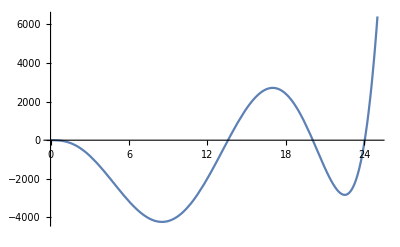

```mathematica
Plot[b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6/.{b->-0.949465061240015,c->-9.26082372139534,d->-46.88166987146679,e->7.915816544040852,f->-0.4254963824358327,g->0.007405044505343755},{x,0,25}]
```

```mathematica
(*Como el área de la parte negativa es superior al 1% del área total, seguimos añadiendo restricciones*)
```

```mathematica
F61[x_]=b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6/.{b->-0.949465061240015,c->-9.26082372139534,d->-46.88166987146679,e->7.915816544040852,f->-0.4254963824358327,g->0.007405044505343755}
```

-0.949465 x-9.26082 x^2-46.8817 x^3+7.91582 x^4-0.425496 x^5+0.00740504 x^6

```mathematica
Solve[F61[x]==0,Reals]
```

{{x→0},{x→13.5711},{x→20.0571},{x→24.0266}}

```mathematica
f[x_]=b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6
```

b x+c x^2+d x^3+e x^4+f x^5+g x^6

```mathematica
f[13.57110791876649/2]
```

6.78555 b+46.0437 c+312.432 d+2120.03 e+14385.6 f+97613.9 g

```mathematica
f[(20.057082730203476+24.026614183346844)/2]
```

22.0418 b+485.843 c+10708.9 d+236044. e+5.20284×10^6 f+1.1468×10^8 g

```mathematica
Minimize[F6[b,c,d,e,f,g],{25 b+25^2c+25^3d+25^4 e+25^5f+25^6g>0,
6.785553959383245 b+46.04374253570163 c+312.43229946795293 d+2120.02622669398 e+14385.552356539656 f+97613.94175083262 g>0,
22.04184845677516 b+485.8430833914415 c+10708.87961788653 d+236043.50167930318 e+5.202835093221754*^6 f+1.1468010267038557*^8 g>0},{b,c,d,e,f,g}]
```

{7.83127×10^19,{b→-24887.1,c→63320.2,d→-17057.6,e→1604.92,f→-62.9532,g→0.882412}}

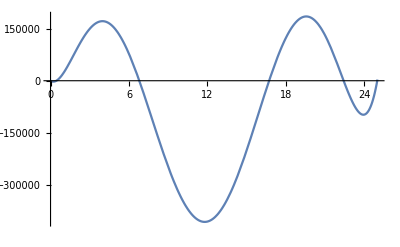

```mathematica
Plot[b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6/.{b->-24887.05084404954,c->63320.2148301044,d->-17057.641995832753,e->1604.9174961522574,f->-62.953196494304365,g->0.8824117005890822},{x,0,25}]
```

```mathematica
(*Como el área de la parte negativa es superior al 1% del área total, seguimos añadiendo restricciones*)
```

```mathematica
F62[x_]=b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6/.{b->-24887.05084404954,c->63320.2148301044,d->-17057.641995832753,e->1604.9174961522574,f->-62.953196494304365,g->0.8824117005890822}
```

-24887.1 x+63320.2 x^2-17057.6 x^3+1604.92 x^4-62.9532 x^5+0.882412 x^6

```mathematica
Solve[F62[x]==0,Reals]
```

{{x→0},{x→0.443949},{x→6.78794},{x→16.7142},{x→22.4123},{x→24.9838}}

```mathematica
f[(0.44394921163086976)/2]
```

0.221975 b+0.0492727 c+0.0109373 d+0.0024278 e+0.00053891 f+0.000119624 g

```mathematica
f[(6.7879351572081745+16.71423390047695)/2]
```

11.7511 b+138.088 c+1622.68 d+19068.3 e+224073. f+2.6331×10^6 g

```mathematica
f[(22.412317668316483+24.983769126373176)/2]
```

23.7108 b+562.2 c+13330.2 d+316069. e+7.49422×10^6 f+1.77694×10^8 g

```mathematica
Minimize[F6[b,c,d,e,f,g],{25 b+25^2c+25^3d+25^4 e+25^5f+25^6g>0,
6.785553959383245 b+46.04374253570163 c+312.43229946795293 d+2120.02622669398 e+14385.552356539656 f+97613.94175083262 g>0,
22.04184845677516 b+485.8430833914415 c+10708.87961788653 d+236043.50167930318 e+5.202835093221754*^6 f+1.1468010267038557*^8 g>0,
0.22197460581543488 b+0.049272725626917695 c+0.010937293848487132 d+0.0024278014907055116 e+0.0005389102788974811 f+0.00011962439672815446 g>0,
11.751084528842561 b+138.087987604003 c+1622.683614752403 d+19068.292320523284 e+224073.11487914858 f+2.6331021135859247*^6 g>0,
23.710752606254346 b+562.1997891549972 c+13330.180115942494 d+316068.60292592336 e+7.494224450581008*^6 f+1.7769370192346865*^8 g>0},{b,c,d,e,f,g}]
```

{2.81663×10^19,{b→-12023.7,c→56772.2,d→-10634.7,e→743.986,f→-22.8374,g→0.259685}}

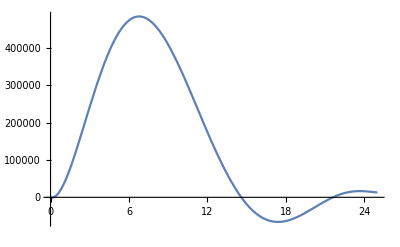

```mathematica
Plot[b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6/.{b->-12023.689367579864,c->56772.24762483751,d->-10634.674592283329,e->743.9856564310305,f->-22.837382225316226,g->0.25968516776535466},{x,0,25}]
```

```mathematica
F63[x_]=b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6/.{b->-12023.689367579864,c->56772.24762483751,d->-10634.674592283329,e->743.9856564310305,f->-22.837382225316226,g->0.25968516776535466}
```

-12023.7 x+56772.2 x^2-10634.7 x^3+743.986 x^4-22.8374 x^5+0.259685 x^6

```mathematica
Solve[F63[x]==0,Reals]
```

{{x→0},{x→0.220779},{x→14.5857},{x→21.5946}}

```mathematica
APN=-Integrate[F63[x],{x,0,0.22077874833721883}]- Integrate[F63[x],{x,14.585700479797955,21.59462123442372}]
```

286464.

```mathematica
AT = -Integrate[F63[x],{x,0,0.22077874833721883}]+Integrate[F63[x],{x,0.22077874833721883,14.585700479797955}]-Integrate[F63[x],{x,14.585700479797955,21.59462123442372}]+Integrate[F63[x],{x,21.59462123442372,25}]
```

4.23089×10^6

```mathematica
APN/AT
```

0.0677076

```mathematica
(*Como el área de la parte negativa es superior al 1% del área total, seguimos añadiendo restricciones*)
```

```mathematica
f[(0.22077874833721883)/2]
```

0.110389 b+0.0121858 c+0.00134518 d+0.000148494 e+0.0000163922 f+1.80952×10^-6 g

```mathematica
f[(14.585700479797955+21.59462123442372)/2]
```

18.0902 b+327.254 c+5920.08 d+107095. e+1.93737×10^6 f+3.50473×10^7 g

```mathematica
Minimize[F6[b,c,d,e,f,g],{25 b+25^2c+25^3d+25^4 e+25^5f+25^6g>0,
6.785553959383245 b+46.04374253570163 c+312.43229946795293 d+2120.02622669398 e+14385.552356539656 f+97613.94175083262 g>0,
22.04184845677516 b+485.8430833914415 c+10708.87961788653 d+236043.50167930318 e+5.202835093221754*^6 f+1.1468010267038557*^8 g>0,
0.22197460581543488 b+0.049272725626917695 c+0.010937293848487132 d+0.0024278014907055116 e+0.0005389102788974811 f+0.00011962439672815446 g>0,
11.751084528842561 b+138.087987604003 c+1622.683614752403 d+19068.292320523284 e+224073.11487914858 f+2.6331021135859247*^6 g>0,
23.710752606254346 b+562.1997891549972 c+13330.180115942494 d+316068.60292592336 e+7.494224450581008*^6 f+1.7769370192346865*^8 g>0,
0.11038937416860942 b+0.012185813929337251 c+0.0013451843733946623 d+0.00014849406112042978 e+0.00001639216647483948 f+1.8095209984251904*^-6 g>0,
18.09016085711084 b+327.25391983614514 c+5920.076050955921 d+107095.12804812212 e+1.9373680934034118*^6 f+3.504730044910186*^7 g>0},{b,c,d,e,f,g}]
```

{3.56124×10^21,{b→32989.9,c→-8781.26,d→916.068,e→-46.9558,f→1.18539,g→-0.0118128}}

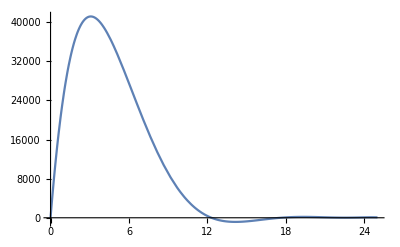

```mathematica
Plot[b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6/.{b->32989.92526787511,c->-8781.26278368602,d->916.0683012880123,e->-46.95575345858268,f->1.1853948099440819,g->-0.01181277560307124},{x,0,25}]
```

```mathematica
F64[x_]=b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6/.{b->32989.92526787511,c->-8781.26278368602,d->916.0683012880123,e->-46.95575345858268,f->1.1853948099440819,g->-0.01181277560307124}
```

32989.9 x-8781.26 x^2+916.068 x^3-46.9558 x^4+1.18539 x^5-0.0118128 x^6

```mathematica
Solve[F64[x]==0,Reals]
```

{{x→0},{x→12.3047},{x→17.5869},{x→25.4149}}

```mathematica
APN1=-Integrate[F64[x],{x,12.304653740649755,17.586937480848952}]
```

2698.39

```mathematica
AT1=Integrate[F64[x],{x,0,12.304653740649755}]-Integrate[F64[x],{x,12.304653740649755,17.586937480848952}]+Integrate[F64[x],{x,17.586937480848952,25}]
```

262259.

```mathematica
APN1/AT1
```

0.010289

```mathematica
(*Como el área de la parte negativa es superior al 1% del área total, seguimos añadiendo restricciones*)
```

```mathematica
f[(12.304653740649755+17.586937480848952)/2]
```

14.9458 b+223.377 c+3338.54 d+49897.2 e+745753. f+1.11459×10^7 g

```mathematica
Minimize[F6[b,c,d,e,f,g],{25 b+25^2c+25^3d+25^4 e+25^5f+25^6g>0,
6.785553959383245 b+46.04374253570163 c+312.43229946795293 d+2120.02622669398 e+14385.552356539656 f+97613.94175083262 g>0,
22.04184845677516 b+485.8430833914415 c+10708.87961788653 d+236043.50167930318 e+5.202835093221754*^6 f+1.1468010267038557*^8 g>0,
0.22197460581543488 b+0.049272725626917695 c+0.010937293848487132 d+0.0024278014907055116 e+0.0005389102788974811 f+0.00011962439672815446 g>0,
11.751084528842561 b+138.087987604003 c+1622.683614752403 d+19068.292320523284 e+224073.11487914858 f+2.6331021135859247*^6 g>0,
23.710752606254346 b+562.1997891549972 c+13330.180115942494 d+316068.60292592336 e+7.494224450581008*^6 f+1.7769370192346865*^8 g>0,
0.11038937416860942 b+0.012185813929337251 c+0.0013451843733946623 d+0.00014849406112042978 e+0.00001639216647483948 f+1.8095209984251904*^-6 g>0,
18.09016085711084 b+327.25391983614514 c+5920.076050955921 d+107095.12804812212 e+1.9373680934034118*^6 f+3.504730044910186*^7 g>0,
14.945795610749354 b+223.37680643829464 c+3338.544093208672 d+49897.19765457135 e+745753.3176943854 f+1.1145876662298515*^7 g>0},{b,c,d,e,f,g}]
```

{3.30029×10^21,{b→5668.25,c→-1442.76,d→146.779,e→-7.44206,f→0.187739,g→-0.00188276}}

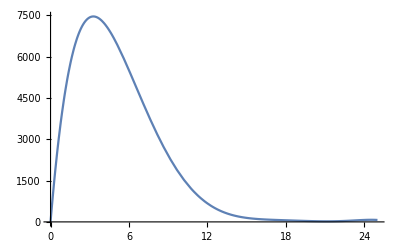

```mathematica
Plot[b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6/.{b->5668.246249093449,c->-1442.7569093565467,d->146.77870255290156,e->-7.442063763941659,f->0.18773863640623967,g->-0.0018827642888264197},{x,0,25}]
```

```mathematica
F65[x_]=b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6/.{b->5668.246249093449,c->-1442.7569093565467,d->146.77870255290156,e->-7.442063763941659,f->0.18773863640623967,g->-0.0018827642888264197}
```

5668.25 x-1442.76 x^2+146.779 x^3-7.44206 x^4+0.187739 x^5-0.00188276 x^6

```mathematica
Solve[F65[x]==0,Reals]
```

{{x→0},{x→25.9066}}

```mathematica
(*Como ya no hay parte negativa, dejamos de añadir restricciones*)
```

```mathematica
(*Obtención de la función de densidad y representación*)
```

```mathematica
Integrate[b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6/.{b->5668.246249093449,c->-1442.7569093565467,d->146.77870255290156,e->-7.442063763941659,f->0.18773863640623967,g->-0.0018827642888264197},{x,0,25}]
```

53009.4

```mathematica
f6[x_]=(b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6)/53009.424362104386/.{b->5668.246249093449,c->-1442.7569093565467,d->146.77870255290156,e->-7.442063763941659,f->0.18773863640623967,g->-0.0018827642888264197}
```

0.0000188646 (5668.25 x-1442.76 x^2+146.779 x^3-7.44206 x^4+0.187739 x^5-0.00188276 x^6)

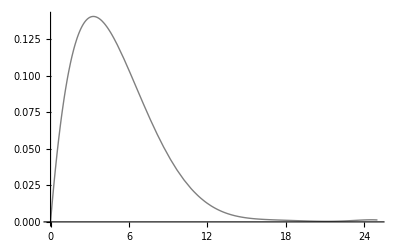

```mathematica
Plot[f6[x],{x,0,25},PlotStyle->{Gray,Thin}]
```

```mathematica
(*Divergencia de Kullback-Leibler*)
```

```mathematica
KL6=N[Integrate[G[x]*Log[G[x]/f6[x]],{x,0,25}]]
```

0.0079062

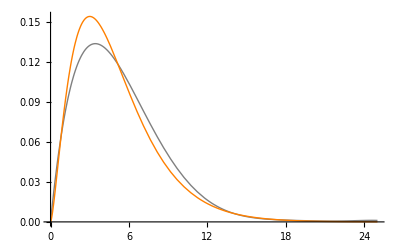

```mathematica
Plot[{f6[x],PDF[ChiSquareDistribution[5],x]},{x,0,25},PlotStyle->{{Gray,Thin},{Orange,Thin}}]
```

```mathematica
(*Verosimilitud*)
```

```mathematica
x6 = Log[f6[datos1]]
```

{-1.98289,-2.01858,-2.07623,-2.15763,-3.43678,-1.97812,-2.1851,-2.05605,-1.96653,-1.98421,-1.96699,-1.96291,-2.35166,-2.26053,9972,-1.97408,-1.98069,-2.17953,-2.30109,-1.98218,-1.97686,-2.02332,-1.99845,-2.2603,-1.96153,-2.4147,-2.05774,-1.97114,-2.25685}
 |  |  |  |

```mathematica
V6 = Apply[Plus,x6]
```

-24378.2

```mathematica
(*BIC*)
```

```mathematica
B6 = -2*V6 + 6*Log[10000]
```

48811.6

### MOP DE GRADO 7

```mathematica
(*Momentos poblacionales*)
```

```mathematica
Integrate[x*(b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7),{x,0,25}]
```

(15625 b)/3+(390625 c)/4+1953125 d+(244140625 e)/6+(6103515625 f)/7+(152587890625 g)/8+(3814697265625 h)/9

```mathematica
Integrate[x^2*(b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7),{x,0,25}]
```

(390625 b)/4+1953125 c+(244140625 d)/6+(6103515625 e)/7+(152587890625 f)/8+(3814697265625 g)/9+(19073486328125 h)/2

```mathematica
Integrate[x^3*(b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7),{x,0,25}]
```

1953125 b+(244140625 c)/6+(6103515625 d)/7+(152587890625 e)/8+(3814697265625 f)/9+(19073486328125 g)/2+(2384185791015625 h)/11

```mathematica
Integrate[x^4*(b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7),{x,0,25}]
```

(244140625 b)/6+(6103515625 c)/7+(152587890625 d)/8+(3814697265625 e)/9+(19073486328125 f)/2+(2384185791015625 g)/11+(59604644775390625 h)/12

```mathematica
Integrate[x^5*(b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7),{x,0,25}]
```

(6103515625 b)/7+(152587890625 c)/8+(3814697265625 d)/9+(19073486328125 e)/2+(2384185791015625 f)/11+(59604644775390625 g)/12+(1490116119384765625 h)/13

```mathematica
Integrate[x^6*(b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7),{x,0,25}]
```

(152587890625 b)/8+(3814697265625 c)/9+(19073486328125 d)/2+(2384185791015625 e)/11+(59604644775390625 f)/12+(1490116119384765625 g)/13+(37252902984619140625 h)/14

```mathematica
Integrate[x^7*(b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7),{x,0,25}]
```

(3814697265625 b)/9+(19073486328125 c)/2+(2384185791015625 d)/11+(59604644775390625 e)/12+(1490116119384765625 f)/13+(37252902984619140625 g)/14+(186264514923095703125 h)/3

```mathematica
(*Función de la suma de las diferencias al cuadrado entre los momentos poblacionales y los muestrales*)
```

```mathematica
F7[b_,c_,d_,e_,f_,g_,h_]= ((15625 b)/3+(390625 c)/4+1953125 d+(244140625 e)/6+(6103515625 f)/7+(152587890625 g)/8+(3814697265625 h)/9-(Apply[Plus,datos1])/10^4)^2+((390625 b)/4+1953125 c+(244140625 d)/6+(6103515625 e)/7+(152587890625 f)/8+(3814697265625 g)/9+(19073486328125 h)/2-(Apply[Plus,datos1^2])/10^4)^2+(1953125 b+(244140625 c)/6+(6103515625 d)/7+(152587890625 e)/8+(3814697265625 f)/9+(19073486328125 g)/2+(2384185791015625 h)/11-(Apply[Plus,datos1^3])/10^4)^2+((244140625 b)/6+(6103515625 c)/7+(152587890625 d)/8+(3814697265625 e)/9+(19073486328125 f)/2+(2384185791015625 g)/11+(59604644775390625 h)/12-(Apply[Plus,datos1^4])/10^4)^2+((6103515625 b)/7+(152587890625 c)/8+(3814697265625 d)/9+(19073486328125 e)/2+(2384185791015625 f)/11+(59604644775390625 g)/12+(1490116119384765625 h)/13-(Apply[Plus,datos1^5])/10^4)^2+((152587890625 b)/8+(3814697265625 c)/9+(19073486328125 d)/2+(2384185791015625 e)/11+(59604644775390625 f)/12+(1490116119384765625 g)/13+(37252902984619140625 h)/14-(Apply[Plus,datos1^6])/10^4)^2+((3814697265625 b)/9+(19073486328125 c)/2+(2384185791015625 d)/11+(59604644775390625 e)/12+(1490116119384765625 f)/13+(37252902984619140625 g)/14+(186264514923095703125 h)/3-(Apply[Plus,datos1^7])/10^4)^2
```

(-5.01025+(15625 b)/3+(390625 c)/4+1953125 d+(244140625 e)/6+(6103515625 f)/7+(152587890625 g)/8+(3814697265625 h)/9)^2+(-35.3233+(390625 b)/4+1953125 c+(244140625 d)/6+(6103515625 e)/7+(152587890625 f)/8+(3814697265625 g)/9+(19073486328125 h)/2)^2+(-320.775+1953125 b+(244140625 c)/6+(6103515625 d)/7+(152587890625 e)/8+(3814697265625 f)/9+(19073486328125 g)/2+(2384185791015625 h)/11)^2+(-3541.44+(244140625 b)/6+(6103515625 c)/7+(152587890625 d)/8+(3814697265625 e)/9+(19073486328125 f)/2+(2384185791015625 g)/11+(59604644775390625 h)/12)^2+(-45551.3+(6103515625 b)/7+(152587890625 c)/8+(3814697265625 d)/9+(19073486328125 e)/2+(2384185791015625 f)/11+(59604644775390625 g)/12+(1490116119384765625 h)/13)^2+(-660392.+(152587890625 b)/8+(3814697265625 c)/9+(19073486328125 d)/2+(2384185791015625 e)/11+(59604644775390625 f)/12+(1490116119384765625 g)/13+(37252902984619140625 h)/14)^2+(-1.05128×10^7+(3814697265625 b)/9+(19073486328125 c)/2+(2384185791015625 d)/11+(59604644775390625 e)/12+(1490116119384765625 f)/13+(37252902984619140625 g)/14+(186264514923095703125 h)/3)^2

```mathematica
Minimize[F7[b,c,d,e,f,g,h],{25 b+25^2c+25^3d+25^4 e+25^5f+25^6g+25^7h>0},{b,c,d,e,f,g,h}]
```

{1.20653×10^27,{b→0.523505,c→-0.487829,d→0.0513995,e→0.357703,f→0.415746,g→-0.100369,h→0.00350531}}

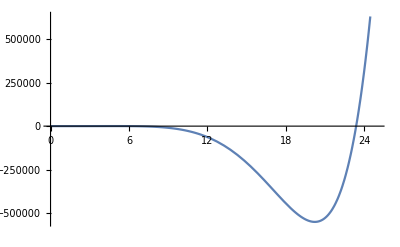

```mathematica
Plot[b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7/.{b->0.5235046209352983,c->-0.4878288565275306,d->0.051399534897090066,e->0.35770309480599033,f->0.41574603842880853,g->-0.10036941726326971,h->0.003505308189545101},{x,0,25}]
```

```mathematica
(*Como el área de la parte negativa es superior al 1% del área total, seguimos añadiendo restricciones*)
```

```mathematica
F71[x_]=b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7/.{b->0.5235046209352983,c->-0.4878288565275306,d->0.051399534897090066,e->0.35770309480599033,f->0.41574603842880853,g->-0.10036941726326971,h->0.003505308189545101}
```

0.523505 x-0.487829 x^2+0.0513995 x^3+0.357703 x^4+0.415746 x^5-0.100369 x^6+0.00350531 x^7

```mathematica
Solve[F71[x]==0,Reals]
```

{{x→0},{x→5.98397},{x→23.3712}}

```mathematica
f[x_]=b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7
```

b x+c x^2+d x^3+e x^4+f x^5+g x^6+h x^7

```mathematica
f[(5.983971482274626+23.371198165034134)/2]
```

14.6776 b+215.431 c+3162.01 d+46410.7 e+681197. f+9.99833×10^6 g+1.46751×10^8 h

```mathematica
Minimize[F7[b,c,d,e,f,g,h],{25 b+25^2c+25^3d+25^4 e+25^5f+25^6g+25^7h>0,
14.67758482365438 b+215.43149625556936 c+3162.0140599779 d+46410.72957891339 e+681197.4201221867 f+9.998332915497923*^6 g+1.4675137946235636*^8 h>0},{b,c,d,e,f,g,h}]
```

{9.03417×10^23,{b→-407.921,c→-1366.01,d→1863.91,e→-257.217,f→13.1395,g→-0.277537,h→0.00192025}}

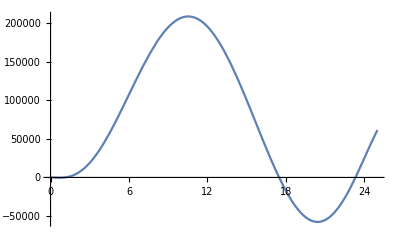

```mathematica
Plot[b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7/.{b->-407.9211258328185,c->-1366.011340750624,d->1863.9133904182263,e->-257.21749792638536,f->13.139453469333043,g->-0.2775368661834832,h->0.0019202515374283592},{x,0,25}]
```

```mathematica
(*Como el área de la parte negativa es superior al 1% del área total, seguimos añadiendo restricciones*)
```

```mathematica
F72[x_]=b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7/.{b->-407.9211258328185,c->-1366.011340750624,d->1863.9133904182263,e->-257.21749792638536,f->13.139453469333043,g->-0.2775368661834832,h->0.0019202515374283592}
```

-407.921 x-1366.01 x^2+1863.91 x^3-257.217 x^4+13.1395 x^5-0.277537 x^6+0.00192025 x^7

```mathematica
Solve[F72[x]==0,Reals]
```

{{x→-0.226444},{x→0},{x→1.08856},{x→17.4771},{x→23.3205},{x→28.3882},{x→74.4835}}

```mathematica
f[(1.0885574815005947)/2]
```

0.544279 b+0.296239 c+0.161237 d+0.0877578 e+0.0477647 f+0.0259973 g+0.0141498 h

```mathematica
f[(17.47714929562902+23.320470100441007)/2]
```

20.3988 b+416.111 c+8488.18 d+173149. e+3.53203×10^6 f+7.20492×10^7 g+1.46972×10^9 h

```mathematica
Minimize[F7[b,c,d,e,f,g,h],{25 b+25^2c+25^3d+25^4 e+25^5f+25^6g+25^7h>0,
14.67758482365438 b+215.43149625556936 c+3162.0140599779 d+46410.72957891339 e+681197.4201221867 f+9.998332915497923*^6 g+1.4675137946235636*^8 h>0,
0.5442787407502974 b+0.2962393476327294 c+0.16123677909023154 d+0.0877577510858651 e+0.0477646782520927 f+0.02599729893139213 g+0.01414977712528716 h>0,
20.398809698035013 b+416.1114370966473 c+8488.178018510376 d+173148.72808263707 e+3.5320279536145246*^6 f+7.204916607392274*^7 g+1.4697172276440704*^9 h>0},{b,c,d,e,f,g,h}]
```

{5.66737×10^26,{b→-349120.,c→-540392.,d→2.416×10^6,e→-467679.,f→34068.8,g→-1093.34,h→13.0269}}

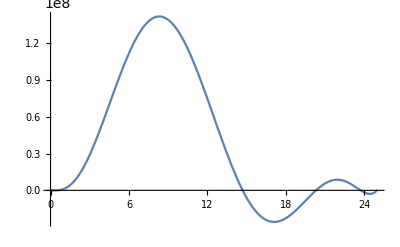

```mathematica
Plot[b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7/.{b->-349119.90928144456,c->-540392.4677455616,d->2.416001146177287*^6,e->-467679.3185970381,f->34068.78226667368,g->-1093.3391001020734,h->13.026869309278553},{x,0,25}]
```

```mathematica
(*Como el área de la parte negativa es superior al 1% del área total, seguimos añadiendo restricciones*)
```

```mathematica
F73[x_]=b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7/.{b->-349119.90928144456,c->-540392.4677455616,d->2.416001146177287*^6,e->-467679.3185970381,f->34068.78226667368,g->-1093.3391001020734,h->13.026869309278553}
```

-349120. x-540392. x^2+2.416×10^6 x^3-467679. x^4+34068.8 x^5-1093.34 x^6+13.0269 x^7

```mathematica
Solve[F73[x]==0,Reals]
```

{{x→-0.278961},{x→0},{x→0.544278},{x→14.6898},{x→20.3012},{x→23.7107},{x→24.9625}}

```mathematica
f[0.544277932282292/2]
```

0.272139 b+0.0740596 c+0.0201545 d+0.00548483 e+0.00149264 f+0.000406204 g+0.000110544 h

```mathematica
f[(14.689837229398243+20.30121668003445)/2]
```

17.4955 b+306.093 c+5355.27 d+93693.2 e+1.63921×10^6 f+2.86789×10^7 g+5.01752×10^8 h

```mathematica
f[(23.710678160651174+24.962486919066524)/2]
```

24.3366 b+592.269 c+14413.8 d+350783. e+8.53686×10^6 f+2.07758×10^8 g+5.05612×10^9 h

```mathematica
Minimize[F7[b,c,d,e,f,g,h],{25 b+25^2c+25^3d+25^4 e+25^5f+25^6g+25^7h>0,
14.67758482365438 b+215.43149625556936 c+3162.0140599779 d+46410.72957891339 e+681197.4201221867 f+9.998332915497923*^6 g+1.4675137946235636*^8 h>0,
0.5442787407502974 b+0.2962393476327294 c+0.16123677909023154 d+0.0877577510858651 e+0.0477646782520927 f+0.02599729893139213 g+0.01414977712528716 h>0,
20.398809698035013 b+416.1114370966473 c+8488.178018510376 d+173148.72808263707 e+3.5320279536145246*^6 f+7.204916607392274*^7 g+1.4697172276440704*^9 h>0,
0.272138966141146 b+0.07405961689237182 c+0.020154507573899423 d+0.005484826854244886 e+0.0014926351095773975 f+0.00040620417554636923 g+0.00011054398437540552 h>0,
17.495526954716347 b+306.09346342320623 c+5355.2664399831865 d+93693.2083504137 e+1.6392120521685176*^6 f+2.867887864321019*^7 g+5.017520943333229*^8 h>0,
24.33658253985885 b+592.2692497193626 c+14413.80948161554 d+350782.8641631367 e+8.536856127274271*^6 f+2.0775790377231008*^8 g+5.056117373462876*^9 h>0},{b,c,d,e,f,g,h}]
```

{8.85077×10^25,{b→145579.,c→-833777.,d→1.15878×10^6,e→-226703.,f→17597.4,g→-611.529,h→7.93893}}

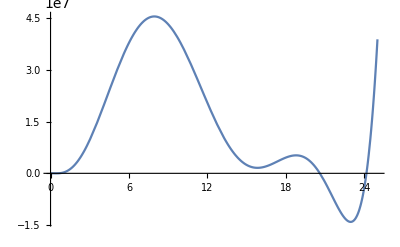

```mathematica
Plot[b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7/.{b->145578.80630329295,c->-833776.9456936351,d->1.158781941300268*^6,e->-226703.0360742623,f->17597.440153087962,g->-611.52925291298,h->7.938929526117139},{x,0,25}]
```

```mathematica
(*Seguimos añadiendo restricciones*)
```

```mathematica
F74[x_]=b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7/.{b->145578.80630329295,c->-833776.9456936351,d->1.158781941300268*^6,e->-226703.0360742623,f->17597.440153087962,g->-611.52925291298,h->7.938929526117139}
```

145579. x-833777. x^2+1.15878×10^6 x^3-226703. x^4+17597.4 x^5-611.529 x^6+7.93893 x^7

```mathematica
Solve[F74[x]==0,Reals]
```

{{x→0},{x→0.272223},{x→0.544232},{x→20.5926},{x→24.1578}}

```mathematica
f[(0.2722226225225536+0.5442324162830794)/2]
```

0.408228 b+0.16665 c+0.068031 d+0.0277721 e+0.0113373 f+0.00462822 g+0.00188937 h

```mathematica
f[(20.592582149323434+24.15777452075175)/2]
```

22.3752 b+500.649 c+11202.1 d+250649. e+5.60832×10^6 f+1.25487×10^8 g+2.8078×10^9 h

```mathematica
Minimize[F7[b,c,d,e,f,g,h],{25 b+25^2c+25^3d+25^4 e+25^5f+25^6g+25^7h>0,
14.67758482365438 b+215.43149625556936 c+3162.0140599779 d+46410.72957891339 e+681197.4201221867 f+9.998332915497923*^6 g+1.4675137946235636*^8 h>0,
0.5442787407502974 b+0.2962393476327294 c+0.16123677909023154 d+0.0877577510858651 e+0.0477646782520927 f+0.02599729893139213 g+0.01414977712528716 h>0,
20.398809698035013 b+416.1114370966473 c+8488.178018510376 d+173148.72808263707 e+3.5320279536145246*^6 f+7.204916607392274*^7 g+1.4697172276440704*^9 h>0,
0.272138966141146 b+0.07405961689237182 c+0.020154507573899423 d+0.005484826854244886 e+0.0014926351095773975 f+0.00040620417554636923 g+0.00011054398437540552 h>0,
17.495526954716347 b+306.09346342320623 c+5355.2664399831865 d+93693.2083504137 e+1.6392120521685176*^6 f+2.867887864321019*^7 g+5.017520943333229*^8 h>0,
24.33658253985885 b+592.2692497193626 c+14413.80948161554 d+350782.8641631367 e+8.536856127274271*^6 f+2.0775790377231008*^8 g+5.056117373462876*^9 h>0,
0.4082275194028165 b+0.16664970759777692 c+0.06803099674184516 d+0.027772125042424545 e+0.011337345714613811 f+0.004628216517688947 g+0.0018893653482753006 h>0,
22.375178335037592 b+500.6486055247356 c+11202.101831803846 d+250649.02621386232 e+5.608316661038682*^6 f+1.2548708545010307*^8 g+2.8077959156901574*^9 h>0},{b,c,d,e,f,g,h}]
```

{1.19043×10^28,{b→8.77553×10^6,c→-1.81949×10^7,d→4.36337×10^6,e→-436584.,f→21954.3,g→-550.688,h→5.49934}}

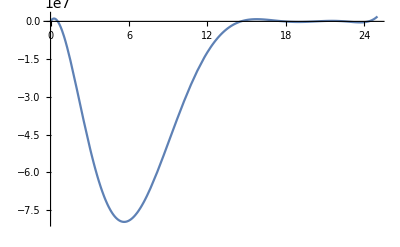

```mathematica
Plot[b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7/.{b->8.775531740791837*^6,c->-1.819491957644379*^7,d->4.363369446576533*^6,e->-436583.8638950543,f->21954.2813658735,g->-550.6877096345454,h->5.499336076242958},{x,0,25}]
```

```mathematica
(*Seguimos añadiendo restricciones*)
```

```mathematica
F75[x_]=b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7/.{b->8.775531740791837*^6,c->-1.819491957644379*^7,d->4.363369446576533*^6,e->-436583.8638950543,f->21954.2813658735,g->-550.6877096345454,h->5.499336076242958}
```

8.77553×10^6 x-1.81949×10^7 x^2+4.36337×10^6 x^3-436584. x^4+21954.3 x^5-550.688 x^6+5.49934 x^7

```mathematica
Solve[F75[x]==0,Reals]
```

{{x→0},{x→0.551277},{x→14.5609},{x→17.8625},{x→20.3034},{x→22.5352},{x→24.3238}}

```mathematica
f[(0.5512771953112116+14.560905526015949)/2]
```

7.55609 b+57.0945 c+431.411 d+3259.78 e+24631.2 f+186116. g+1.40631×10^6 h

```mathematica
f[(17.86251841951915+20.30342137946544)/2]
```

19.083 b+364.16 c+6949.25 d+132612. e+2.53064×10^6 f+4.82921×10^7 g+9.21556×10^8 h

```mathematica
f[(22.535163377836607+24.323840111201612)/2]
```

23.4295 b+548.942 c+12861.4 d+301337. e+7.06017×10^6 f+1.65416×10^8 g+3.87562×10^9 h

```mathematica
Minimize[F7[b,c,d,e,f,g,h],{25 b+25^2c+25^3d+25^4 e+25^5f+25^6g+25^7h>0,
14.67758482365438 b+215.43149625556936 c+3162.0140599779 d+46410.72957891339 e+681197.4201221867 f+9.998332915497923*^6 g+1.4675137946235636*^8 h>0,
0.5442787407502974 b+0.2962393476327294 c+0.16123677909023154 d+0.0877577510858651 e+0.0477646782520927 f+0.02599729893139213 g+0.01414977712528716 h>0,
20.398809698035013 b+416.1114370966473 c+8488.178018510376 d+173148.72808263707 e+3.5320279536145246*^6 f+7.204916607392274*^7 g+1.4697172276440704*^9 h>0,
0.272138966141146 b+0.07405961689237182 c+0.020154507573899423 d+0.005484826854244886 e+0.0014926351095773975 f+0.00040620417554636923 g+0.00011054398437540552 h>0,
17.495526954716347 b+306.09346342320623 c+5355.2664399831865 d+93693.2083504137 e+1.6392120521685176*^6 f+2.867887864321019*^7 g+5.017520943333229*^8 h>0,
24.33658253985885 b+592.2692497193626 c+14413.80948161554 d+350782.8641631367 e+8.536856127274271*^6 f+2.0775790377231008*^8 g+5.056117373462876*^9 h>0,
0.4082275194028165 b+0.16664970759777692 c+0.06803099674184516 d+0.027772125042424545 e+0.011337345714613811 f+0.004628216517688947 g+0.0018893653482753006 h>0,
22.375178335037592 b+500.6486055247356 c+11202.101831803846 d+250649.02621386232 e+5.608316661038682*^6 f+1.2548708545010307*^8 g+2.8077959156901574*^9 h>0,
7.55609136066358 b+57.09451665069479 c+431.4113840055779 d+3259.7838315764648 e+24631.224447405748 f+186115.78224960816 g+1.4063078543394085*^6 h>0,
19.082969899492298 b+364.1597401849291 c+6949.2493605559375 d+132612.31637155506 e+2.530636841620335*^6 f+4.82920666751871*^7 g+9.215560547468706*^8 h>0,
23.429501744519108 b+548.9415519964239 c+12861.42705013924 d+301336.8275082425 e+7.060171725792222*^6 f+1.6541630576605335*^8 g+3.875621624517653*^9 h>0},{b,c,d,e,f,g,h}]
```

{1.56185×10^28,{b→0.630721,c→0.457676,d→0.221456,e→0.865701,f→0.0713487,g→-0.0105274,h→0.00025136}}

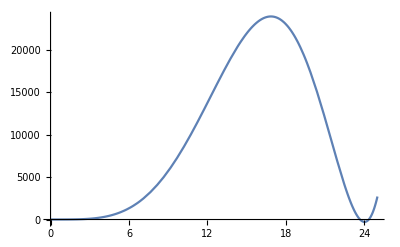

```mathematica
Plot[b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7/.{b->0.630720829830902,c->0.4576758664436933,d->0.22145637715844113,e->0.8657005091811474,f->0.07134873801262585,g->-0.010527410796547402,h->0.0002513603855171246},{x,0,25}]
```

```mathematica
F76[x_]=b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7/.{b->0.630720829830902,c->0.4576758664436933,d->0.22145637715844113,e->0.8657005091811474,f->0.07134873801262585,g->-0.010527410796547402,h->0.0002513603855171246}
```

0.630721 x+0.457676 x^2+0.221456 x^3+0.865701 x^4+0.0713487 x^5-0.0105274 x^6+0.00025136 x^7

```mathematica
Solve[F76[x]==0,Reals]
```

{{x→-5.89634},{x→-0.797372},{x→0},{x→23.6694},{x→24.3365}}

```mathematica
APN=-Integrate[F76[x],{x,23.66935428830768,24.336540616798434}]
```

124.807

```mathematica
AT=Integrate[F76[x],{x,0,23.66935428830768}]-Integrate[F76[x],{x,23.66935428830768,24.336540616798434}]+Integrate[F76[x],{x,24.336540616798434,25}]
```

233611.

```mathematica
APN/AT
```

0.00053425

```mathematica
(*Como el área de la parte negativa es inferior al 1% del área total, dejamos de añadir restricciones*)
```

```mathematica
(*Obtención de la densidad y representación gráfica*)
```

```mathematica
FindMinimum[F76[x],{x,23}]
```

{-280.808,{x→24.014}}

```mathematica
Integrate[b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+280.80786711955443/.{b->0.630720829830902,c->0.4576758664436933,d->0.22145637715844113,e->0.8657005091811474,f->0.07134873801262585,g->-0.010527410796547402,h->0.0002513603855171246},{x,0,25}]
```

240382.

```mathematica
f7[x_]=(b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+280.80786711955443)/240381.6348616309/.{b->0.630720829830902,c->0.4576758664436933,d->0.22145637715844113,e->0.8657005091811474,f->0.07134873801262585,g->-0.010527410796547402,h->0.0002513603855171246}
```

4.16005×10^-6 (280.808+0.630721 x+0.457676 x^2+0.221456 x^3+0.865701 x^4+0.0713487 x^5-0.0105274 x^6+0.00025136 x^7)

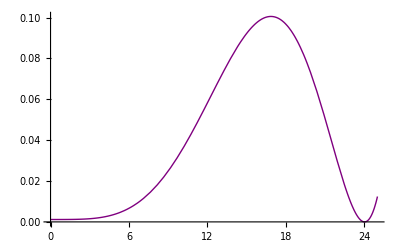

```mathematica
Plot[f7[x],{x,0,25},PlotStyle->{Purple,Thin}]
```

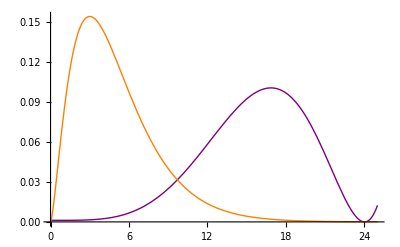

```mathematica
Plot[{f7[x],PDF[ChiSquareDistribution[5],x]},{x,0,25},PlotStyle->{{Purple,Thin},{Orange,Thin}}]
```

```mathematica
(*Divergencia de Kullback-Leibler*)
```

```mathematica
KL7=N[Integrate[G[x]*Log[G[x]/f7[x]],{x,0,25}]]
```

3.08208

```mathematica
(*Verosimilitud*)
```

```mathematica
x7 = Log[f7[datos1]]
```

{-6.09648,-6.62974,-5.61447,-5.32119,-3.38468,-6.54025,-5.23506,-6.66717,-6.4756,-6.08676,-6.47944,-6.30756,-4.80009,-5.02204,-6.7305,9971,-6.52286,-6.54974,-6.71737,-6.73426,-6.55483,-6.14432,-6.63581,-5.99182,-5.02264,-6.39713,-4.66389,-6.66842,-6.50754,-6.72974}
 |  |  |  |

```mathematica
V7 = Apply[Plus,x7]
```

-55022.7

```mathematica
(*BIC*)
```

```mathematica
B7 = -2*V7 + 7*Log[10000]
```

110110.

### MOP DE GRADO 8

```mathematica
(*Momentos poblacionales*)
```

```mathematica
Integrate[x*(b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8),{x,0,25}]
```

(15625 b)/3+(390625 c)/4+1953125 d+(244140625 e)/6+(6103515625 f)/7+(152587890625 g)/8+(3814697265625 h)/9+(19073486328125 i)/2

```mathematica
Integrate[x^2*(b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8),{x,0,25}]
```

(390625 b)/4+1953125 c+(244140625 d)/6+(6103515625 e)/7+(152587890625 f)/8+(3814697265625 g)/9+(19073486328125 h)/2+(2384185791015625 i)/11

```mathematica
Integrate[x^3*(b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8),{x,0,25}]
```

1953125 b+(244140625 c)/6+(6103515625 d)/7+(152587890625 e)/8+(3814697265625 f)/9+(19073486328125 g)/2+(2384185791015625 h)/11+(59604644775390625 i)/12

```mathematica
Integrate[x^4*(b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8),{x,0,25}]
```

(244140625 b)/6+(6103515625 c)/7+(152587890625 d)/8+(3814697265625 e)/9+(19073486328125 f)/2+(2384185791015625 g)/11+(59604644775390625 h)/12+(1490116119384765625 i)/13

```mathematica
Integrate[x^5*(b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8),{x,0,25}]
```

(6103515625 b)/7+(152587890625 c)/8+(3814697265625 d)/9+(19073486328125 e)/2+(2384185791015625 f)/11+(59604644775390625 g)/12+(1490116119384765625 h)/13+(37252902984619140625 i)/14

```mathematica
Integrate[x^6*(b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8),{x,0,25}]
```

(152587890625 b)/8+(3814697265625 c)/9+(19073486328125 d)/2+(2384185791015625 e)/11+(59604644775390625 f)/12+(1490116119384765625 g)/13+(37252902984619140625 h)/14+(186264514923095703125 i)/3

```mathematica
Integrate[x^7*(b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8),{x,0,25}]
```

(3814697265625 b)/9+(19073486328125 c)/2+(2384185791015625 d)/11+(59604644775390625 e)/12+(1490116119384765625 f)/13+(37252902984619140625 g)/14+(186264514923095703125 h)/3+(23283064365386962890625 i)/16

```mathematica
Integrate[x^8*(b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8),{x,0,25}]
```

(19073486328125 b)/2+(2384185791015625 c)/11+(59604644775390625 d)/12+(1490116119384765625 e)/13+(37252902984619140625 f)/14+(186264514923095703125 g)/3+(23283064365386962890625 h)/16+(582076609134674072265625 i)/17

```mathematica
F8[b_,c_,d_,e_,f_,g_,h_,i_]= ((15625 b)/3+(390625 c)/4+1953125 d+(244140625 e)/6+(6103515625 f)/7+(152587890625 g)/8+(3814697265625 h)/9+(19073486328125 i)/2-(Apply[Plus,datos1])/10^4)^2+((390625 b)/4+1953125 c+(244140625 d)/6+(6103515625 e)/7+(152587890625 f)/8+(3814697265625 g)/9+(19073486328125 h)/2+(2384185791015625 i)/11-(Apply[Plus,datos1^2])/10^4)^2+(1953125 b+(244140625 c)/6+(6103515625 d)/7+(152587890625 e)/8+(3814697265625 f)/9+(19073486328125 g)/2+(2384185791015625 h)/11+(59604644775390625 i)/12-(Apply[Plus,datos1^3])/10^4)^2+((244140625 b)/6+(6103515625 c)/7+(152587890625 d)/8+(3814697265625 e)/9+(19073486328125 f)/2+(2384185791015625 g)/11+(59604644775390625 h)/12+(1490116119384765625 i)/13-(Apply[Plus,datos1^4])/10^4)^2+((6103515625 b)/7+(152587890625 c)/8+(3814697265625 d)/9+(19073486328125 e)/2+(2384185791015625 f)/11+(59604644775390625 g)/12+(1490116119384765625 h)/13+(37252902984619140625 i)/14-(Apply[Plus,datos1^5])/10^4)^2+((152587890625 b)/8+(3814697265625 c)/9+(19073486328125 d)/2+(2384185791015625 e)/11+(59604644775390625 f)/12+(1490116119384765625 g)/13+(37252902984619140625 h)/14+(186264514923095703125 i)/3-(Apply[Plus,datos1^6])/10^4)^2+((3814697265625 b)/9+(19073486328125 c)/2+(2384185791015625 d)/11+(59604644775390625 e)/12+(1490116119384765625 f)/13+(37252902984619140625 g)/14+(186264514923095703125 h)/3+(23283064365386962890625 i)/16-(Apply[Plus,datos1^7])/10^4)^2+((19073486328125 b)/2+(2384185791015625 c)/11+(59604644775390625 d)/12+(1490116119384765625 e)/13+(37252902984619140625 f)/14+(186264514923095703125 g)/3+(23283064365386962890625 h)/16+(582076609134674072265625 i)/17-(Apply[Plus,datos1^8])/10^4)^2
```

(-5.01025+(15625 b)/3+(390625 c)/4+1953125 d+(244140625 e)/6+(6103515625 f)/7+(152587890625 g)/8+(3814697265625 h)/9+(19073486328125 i)/2)^2+(-35.3233+(390625 b)/4+1953125 c+(244140625 d)/6+(6103515625 e)/7+(152587890625 f)/8+(3814697265625 g)/9+(19073486328125 h)/2+(2384185791015625 i)/11)^2+(-320.775+1953125 b+(244140625 c)/6+(6103515625 d)/7+(152587890625 e)/8+(3814697265625 f)/9+(19073486328125 g)/2+(2384185791015625 h)/11+(59604644775390625 i)/12)^2+(-3541.44+(244140625 b)/6+(6103515625 c)/7+(152587890625 d)/8+(3814697265625 e)/9+(19073486328125 f)/2+(2384185791015625 g)/11+(59604644775390625 h)/12+(1490116119384765625 i)/13)^2+(-45551.3+(6103515625 b)/7+(152587890625 c)/8+(3814697265625 d)/9+(19073486328125 e)/2+(2384185791015625 f)/11+(59604644775390625 g)/12+(1490116119384765625 h)/13+(37252902984619140625 i)/14)^2+(-660392.+(152587890625 b)/8+(3814697265625 c)/9+(19073486328125 d)/2+(2384185791015625 e)/11+(59604644775390625 f)/12+(1490116119384765625 g)/13+(37252902984619140625 h)/14+(186264514923095703125 i)/3)^2+(-1.05128×10^7+(3814697265625 b)/9+(19073486328125 c)/2+(2384185791015625 d)/11+(59604644775390625 e)/12+(1490116119384765625 f)/13+(37252902984619140625 g)/14+(186264514923095703125 h)/3+(23283064365386962890625 i)/16)^2+(-1.79987×10^8+(19073486328125 b)/2+(2384185791015625 c)/11+(59604644775390625 d)/12+(1490116119384765625 e)/13+(37252902984619140625 f)/14+(186264514923095703125 g)/3+(23283064365386962890625 h)/16+(582076609134674072265625 i)/17)^2

```mathematica
Minimize[F8[b,c,d,e,f,g,h,i],{25 b+25^2c+25^3d+25^4 e+25^5f+25^6g+25^7h+25^8i>0},{b,c,d,e,f,g,h,i}]
```

{7.85939×10^28,{b→-0.682048,c→0.733499,d→-0.432959,e→0.416595,f→0.378965,g→-0.232459,h→0.0175483,i→-0.000355064}}

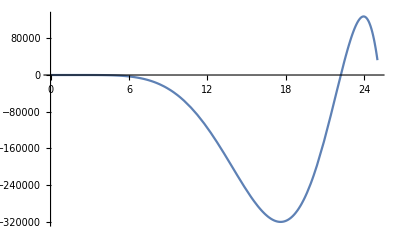

```mathematica
Plot[b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8/.{b->-0.6820478621769754,c->0.7334994003962207,d->-0.43295886024711,e->0.4165947334930259,f->0.3789653849982679,g->-0.23245894117060306,h->0.01754829599019616,i->-0.0003550639854360703},{x,0,25}]
```

```mathematica
(*Como el área de la parte negativa es superior al 1% del área total, seguimos añadiendo restricciones*)
```

```mathematica
f[x_]=b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8
```

b x+c x^2+d x^3+e x^4+f x^5+g x^6+h x^7+i x^8

```mathematica
F81[x_]=b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8/.{b->-0.6820478621769754,c->0.7334994003962207,d->-0.43295886024711,e->0.4165947334930259,f->0.3789653849982679,g->-0.23245894117060306,h->0.01754829599019616,i->-0.0003550639854360703}
```

-0.682048 x+0.733499 x^2-0.432959 x^3+0.416595 x^4+0.378965 x^5-0.232459 x^6+0.0175483 x^7-0.000355064 x^8

```mathematica
Solve[F81[x]==0,Reals]
```

{{x→-1.53668},{x→0},{x→0.861207},{x→2.65388},{x→22.1972},{x→25.146}}

```mathematica
f[0.8612073921962254/2]
```

0.430604 b+0.18542 c+0.0798423 d+0.0343804 e+0.0148043 f+0.0063748 g+0.00274501 h+0.00118201 i

```mathematica
f[(2.653881239540631+22.19722101951365)/2]
```

12.4256 b+154.394 c+1918.43 d+23837.6 e+296195. f+3.68039×10^6 g+4.57309×10^7 h+5.68231×10^8 i

```mathematica
Minimize[F8[b,c,d,e,f,g,h,i],{25 b+25^2c+25^3d+25^4 e+25^5f+25^6g+25^7h+25^8i>0,
0.4306036960981127 b+0.18541954309335582 c+0.0798423405848223 d+0.03438040696094884 e+0.014804330310741852 f+0.006374799350062762 g+0.002745012162020872 h+0.0011820123828004592 i>0,
12.42555112952714 b+154.39432087249318 c+1918.4345281097833 d+23837.606317678383 e+296195.3961058519 f+3.6803910386438067*^6 g+4.573088702732211*^7 h+5.682314749566203*^8 i>0},{b,c,d,e,f,g,h,i}]
```

{1.93469×10^27,{b→0.240843,c→-0.329238,d→-0.228185,e→-0.121642,f→-0.580359,g→0.274835,h→-0.0215819,i→0.000464409}}

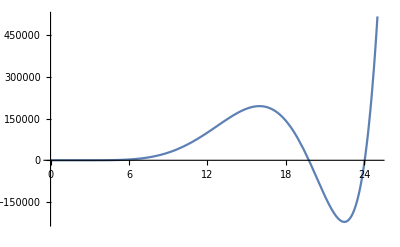

```mathematica
Plot[b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8/.{b->0.24084306386941795,c->-0.32923758181239854,d->-0.22818545849698793,e->-0.12164196224667563,f->-0.5803593263650608,g->0.2748345552997487,h->-0.021581916081271458,i->0.00046440936610473793},{x,0,25}]
```

```mathematica
(*Seguimos añadiendo restricciones*)
```

```mathematica
F82[x_]=b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8/.{b->0.24084306386941795,c->-0.32923758181239854,d->-0.22818545849698793,e->-0.12164196224667563,f->-0.5803593263650608,g->0.2748345552997487,h->-0.021581916081271458,i->0.00046440936610473793}
```

0.240843 x-0.329238 x^2-0.228185 x^3-0.121642 x^4-0.580359 x^5+0.274835 x^6-0.0215819 x^7+0.000464409 x^8

```mathematica
Solve[F82[x]==0,Reals]
```

{{x→-0.848669},{x→0},{x→0.471021},{x→3.06525},{x→19.7568},{x→24.024}}

```mathematica
f[(0.47102127289521245+0.47102127289521245)/2]
```

0.471021 b+0.221861 c+0.104501 d+0.0492223 e+0.0231848 f+0.0109205 g+0.0051438 h+0.00242284 i

```mathematica
f[(19.75675268107195+24.023996221322918)/2]
```

21.8904 b+479.188 c+10489.6 d+229622. e+5.0265×10^6 f+1.10032×10^8 g+2.40864×10^9 h+5.27261×10^10 i

```mathematica
Minimize[F8[b,c,d,e,f,g,h,i],{25 b+25^2c+25^3d+25^4 e+25^5f+25^6g+25^7h+25^8i>0,
0.4306036960981127 b+0.18541954309335582 c+0.0798423405848223 d+0.03438040696094884 e+0.014804330310741852 f+0.006374799350062762 g+0.002745012162020872 h+0.0011820123828004592 i>0,
12.42555112952714 b+154.39432087249318 c+1918.4345281097833 d+23837.606317678383 e+296195.3961058519 f+3.6803910386438067*^6 g+4.573088702732211*^7 h+5.682314749566203*^8 i>0,
0.47102127289521245 b+0.2218610395198262 c+0.10450126924048357 d+0.04922232085681788 e+0.023184760224834924 f+0.010920515272872038 g+0.005143795004499796 h+0.0024228368705315286 i>0,
21.890374451197435 b+479.1884936136374 c+10489.615557907753 d+229621.612411707 e+5.026503077779991*^6 f+1.1003203455270039*^8 g+2.408642437985706*^9 h+5.272608488655219*^10 i>0},{b,c,d,e,f,g,h,i}]
```

{1.71715×10^25,{b→-51152.1,c→242078.,d→-319146.,e→79863.2,f→-8575.39,g→463.402,h→-12.4358,i→0.132072}}

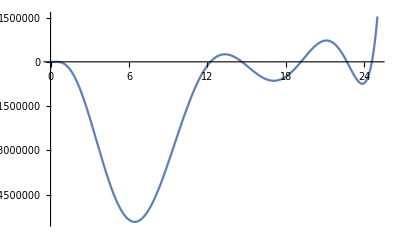

```mathematica
Plot[b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8/.{b->-51152.09566431793,c->242077.87371974747,d->-319145.7230544685,e->79863.19809942962,f->-8575.387162474828,g->463.40212027011455,h->-12.435837118013891,i->0.13207249676284746},{x,0,25}]
```

```mathematica
(*Seguimos añadiendo restricciones*)
```

```mathematica
F94[x_]=b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8/.{b->-51152.09566431793,c->242077.87371974747,d->-319145.7230544685,e->79863.19809942962,f->-8575.387162474828,g->463.40212027011455,h->-12.435837118013891,i->0.13207249676284746}
```

-51152.1 x+242078. x^2-319146. x^3+79863.2 x^4-8575.39 x^5+463.402 x^6-12.4358 x^7+0.132072 x^8

```mathematica
Solve[F94[x]==0,Reals]
```

{{x→0},{x→0.430593},{x→0.471026},{x→12.2328},{x→14.635},{x→19.1513},{x→22.6655},{x→24.573}}

```mathematica
f[(0.4305927821815463)/2]
```

0.215296 b+0.0463525 c+0.00997953 d+0.00214856 e+0.000462577 f+0.0000995911 g+0.0000214416 h+4.6163×10^-6 i

```mathematica
f[(0.4710262825192665+12.232766897876962)/2]
```

6.3519 b+40.3466 c+256.277 d+1627.85 e+10339.9 f+65678.1 g+417180. h+2.64989×10^6 i

```mathematica
f[(14.635037599013579+19.151251348369144)/2]
```

16.8931 b+285.378 c+4820.94 d+81440.8 e+1.37579×10^6 f+2.32414×10^7 g+3.92621×10^8 h+6.6326×10^9 i

```mathematica
f[(22.665500492970303+24.57299795126127)/2]
```

23.6192 b+557.869 c+13176.4 d+311218. e+7.35073×10^6 f+1.73619×10^8 g+4.10074×10^9 h+9.68565×10^10 i

```mathematica
Minimize[F8[b,c,d,e,f,g,h,i],{25 b+25^2c+25^3d+25^4 e+25^5f+25^6g+25^7h+25^8i>0,
0.4306036960981127 b+0.18541954309335582 c+0.0798423405848223 d+0.03438040696094884 e+0.014804330310741852 f+0.006374799350062762 g+0.002745012162020872 h+0.0011820123828004592 i>0,
12.42555112952714 b+154.39432087249318 c+1918.4345281097833 d+23837.606317678383 e+296195.3961058519 f+3.6803910386438067*^6 g+4.573088702732211*^7 h+5.682314749566203*^8 i>0,
0.21529639109077314 b+0.04635253601671114 c+0.009979533722302989 d+0.0021485575951805036 e+0.00046257669629303275 f+0.00009959109331458254 g+0.000021441602975414045 h+4.616299739807829*^-6 i>0,
6.351896590198114 b+40.34659029257043 c+256.2773693054985 d+1627.8473482365387 e+10339.918020626712 f+65678.09001814686 g+417180.4360369918 h+2.649886989160731*^6 i>0,
16.89314447369136 b+285.378330209009 c+4820.937361881589 d+81440.79135288218 e+1.3757910543759929*^6 f+2.3241437047185816*^7 g+3.9262095381431276*^8 h+6.632602496183689*^9 i>0,
23.619249222115787 b+557.8689338164172 c+13176.445381085976 d+311217.74731746607 e+7.3507295362366885*^6 f+1.7361871288074195*^8 g+4.1007436491532087*^9 h+9.685648624535815*^10 i>0},{b,c,d,e,f,g,h,i}]
```

{1.75042×10^33,{b→0.362641,c→0.423294,d→-0.294114,e→-0.251385,f→0.0928752,g→0.157209,h→-0.0135964,i→0.000287658}}

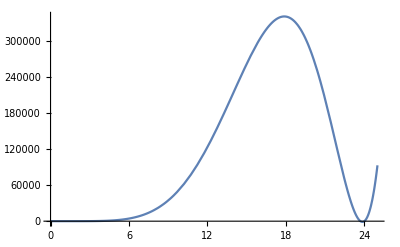

```mathematica
Plot[b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8/.{b->0.3626408228761059,c->0.4232940517879681,d->-0.29411388974091124,e->-0.25138498144826854,f->0.09287517516702312,g->0.15720899251557469,h->-0.013596390826292888,i->0.00028765841450052157},{x,0,25}]
```

```mathematica
F83[x_]=b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8/.{b->0.3626408228761059,c->0.4232940517879681,d->-0.29411388974091124,e->-0.25138498144826854,f->0.09287517516702312,g->0.15720899251557469,h->-0.013596390826292888,i->0.00028765841450052157}
```

0.362641 x+0.423294 x^2-0.294114 x^3-0.251385 x^4+0.0928752 x^5+0.157209 x^6-0.0135964 x^7+0.000287658 x^8

```mathematica
Solve[F83[x]==0,Reals]
```

{{x→-0.704986},{x→0},{x→23.699},{x→23.9969}}

```mathematica
APN = -Integrate[F83[x],{x,23.69900573103336,23.9969054981663}]
```

236.677

```mathematica
AT= Integrate[F83[x],{x,0,23.69900573103336}] -Integrate[F83[x],{x,23.69900573103336,23.9969054981663}]+ Integrate[F83[x],{x,23.9969054981663,25}]
```

2.9325×10^6

```mathematica
APN/AT
```

0.0000807081

```mathematica
(*Como el área de la parte negativa ya es inferior al 1% del área total, dejamos de añadir restricciones*)
```

```mathematica
(*Obtención de la densidad y representación gráfica*)
```

```mathematica
FindMinimum[F83[x],{x,23.8}]
```

{-1192.,{x→23.8507}}

```mathematica
Integrate[b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+1192.0033644922078/.{b->0.3626408228761059,c->0.4232940517879681,d->-0.29411388974091124,e->-0.25138498144826854,f->0.09287517516702312,g->0.15720899251557469,h->-0.013596390826292888,i->0.00028765841450052157},{x,0,25}]
```

2.96183×10^6

```mathematica
f8[x_]=(b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+1192.0033644922078)/2.9618285942439213*^6/.{b->0.3626408228761059,c->0.4232940517879681,d->-0.29411388974091124,e->-0.25138498144826854,f->0.09287517516702312,g->0.15720899251557469,h->-0.013596390826292888,i->0.00028765841450052157}
```

3.37629×10^-7 (1192.+0.362641 x+0.423294 x^2-0.294114 x^3-0.251385 x^4+0.0928752 x^5+0.157209 x^6-0.0135964 x^7+0.000287658 x^8)

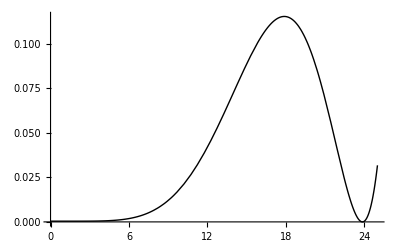

```mathematica
Plot[f8[x],{x,0,25},PlotStyle->{Black,Thin}]
```

```mathematica
(*Divergencia de Kullback-Leibler*)
```

```mathematica
KL8=N[Integrate[G[x]*Log[G[x]/f8[x]],{x,0,25}]]
```

4.21896

```mathematica
(*Evolución densidades*)
```

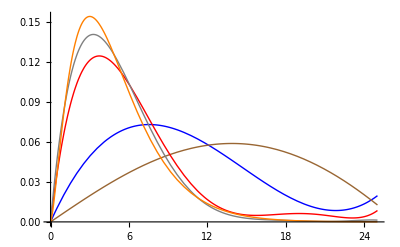

```mathematica
Plot[{f3[x],f4[x],f5[x],f6[x],PDF[ChiSquareDistribution[5],x]},{x,0,25},PlotStyle->{{Blue,Thin},{Brown,Thin},{Red,Thin},{Gray,Thin},{Orange,Thin}}]
```

### GRÁFICO DIVERGENCIAS

```mathematica
DKL = {{{3,0.5445778101542702}},{{4,1.2702688525921237}},{{5,0.048222383291566}},{{6,0.007906196369347772}}}
```

{{{3,0.544578}},{{4,1.27027}},{{5,0.0482224}},{{6,0.0079062}}}

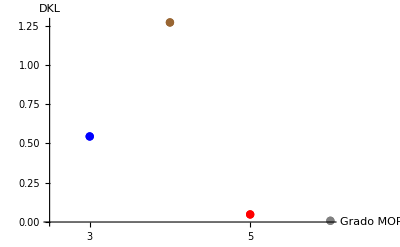

```mathematica
g1 =ListPlot[DKL,PlotStyle->{{Blue,Thin,PointSize[0.015]},{Brown,Thin,PointSize[0.015]},{Red,Thin,PointSize[0.015]},{Gray,Thin,PointSize[0.015]},{Purple,Thin,PointSize[0.015]}},AxesLabel->{"Grado MOP","DKL"},AxesOrigin->{2.5,0},AxesStyle->Directive[Black, 12],Ticks->{{3,4,5,6,7,8}, Automatic},PlotRange->Full]
```

```mathematica
DKL1 =  {{3,0.5445778101542702},{4,1.2702688525921237},{5,0.048222383291566},{6,0.007906196369347772}}
```

{{3,0.544578},{4,1.27027},{5,0.0482224},{6,0.0079062}}

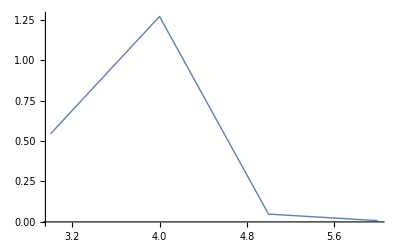

```mathematica
g2 = ListLinePlot[DKL1,PlotStyle->Thin]
```

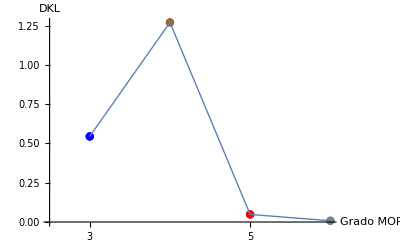

```mathematica
Show[g1,g2]
```

### GRÁFICO VEROSIMILITUDES

```mathematica
V = {{{3,-29693.56614494459}},{{4,-36930.21290154075}},{{5,-24765.983398273434}},{{6,-24378.172766419568}}}
```

{{{3,-29693.6}},{{4,-36930.2}},{{5,-24766.}},{{6,-24378.2}}}

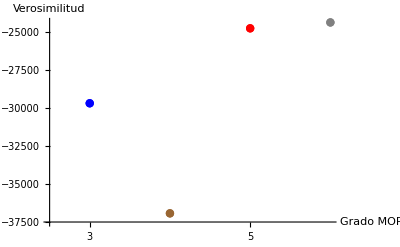

```mathematica
l1 =ListPlot[V,PlotStyle->{{Blue,Thin,PointSize[0.015]},{Brown,Thin,PointSize[0.015]},{Red,Thin,PointSize[0.015]},{Gray,Thin,PointSize[0.015]},{Purple,Thin,PointSize[0.015]}},AxesLabel->{"Grado MOP","Verosimilitud"},AxesOrigin->{2.5,-37500},AxesStyle->Directive[Black, 12],Ticks->{{3,4,5,6,7,8}, Automatic},PlotRange->Full]
```

```mathematica
V1={{3,-29693.56614494459},{4,-36930.21290154075},{5,-24765.983398273434},{6,-24378.172766419568}}
```

{{3,-29693.6},{4,-36930.2},{5,-24766.},{6,-24378.2}}

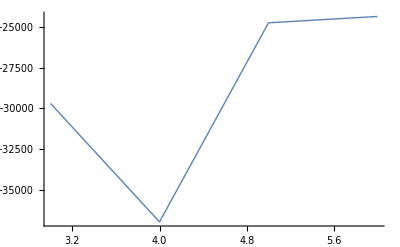

```mathematica
l2 = ListLinePlot[V1,PlotStyle->Thin]
```

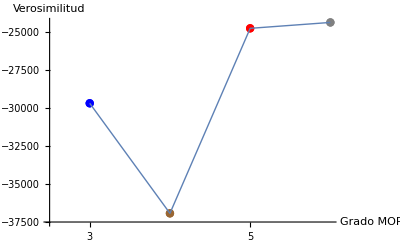

```mathematica
Show[l1,l2]
```

```mathematica
(*Verosimilitudes con otra muestra*)
```

```mathematica
SeedRandom[9999]
```

```mathematica
data2 = RandomVariate[ChiSquareDistribution[5],10^4]
```

{3.96605,12.2747,13.5228,1.76819,10.8582,1.05163,3.81019,1.24328,5.1667,2.84983,6.13444,3.98101,2.4274,10.0782,2.79229,9970,5.16258,3.29537,1.09189,6.60263,4.9086,2.30719,4.74205,2.31849,5.09778,1.41025,2.81431,2.57358,2.38694,8.57604,0.704001}
 |  |  |  |

```mathematica
Select[data2,# >25&]
```

{25.4356}

```mathematica
Position[data2,25.435577294668327]
```

{{485}}

```mathematica
data21 = Delete[data2,485]
```

{3.96605,12.2747,13.5228,1.76819,10.8582,1.05163,3.81019,1.24328,5.1667,2.84983,6.13444,3.98101,2.4274,10.0782,2.79229,9969,5.16258,3.29537,1.09189,6.60263,4.9086,2.30719,4.74205,2.31849,5.09778,1.41025,2.81431,2.57358,2.38694,8.57604,0.704001}
 |  |  |  |

```mathematica
y3 = Log[f3[data21]]
```

{-2.83185,-2.87433,-3.02551,-3.41519,-2.7456,-3.86663,-2.85519,-3.71723,-2.70124,-3.04529,-2.64415,-2.8297,-3.1631,-2.69329,9971,-2.94596,-3.83283,-2.6284,-2.72297,-3.20193,-2.73867,-3.19817,-2.70675,-3.60704,-3.05421,-3.11927,-3.17588,-2.62985,-4.23568}
 |  |  |  |

```mathematica
y4=Log[f4[data21]]
```

{-3.66528,-2.84948,-2.83357,-4.445,-2.89271,-4.96029,-3.70266,-4.79379,-3.42545,-3.97876,-3.27838,-3.66179,-4.13424,-2.92864,9971,-3.83962,-4.9229,-3.2183,-3.47085,-4.18376,-3.50175,-4.17899,-3.43729,-4.66873,-3.99085,-4.07738,-4.15061,-3.025,-5.36039}
 |  |  |  |

```mathematica
y5=Log[f5[data21]]
```

{-2.08565,-4.21952,-4.79359,-2.33553,-3.60209,-2.68911,-2.08346,-2.56542,-2.16301,-2.12293,-2.29007,-2.08596,-2.17786,-3.30502,9971,-2.09211,-2.66069,-2.3695,-2.13824,-2.19914,-2.12447,-2.19702,-2.156,-2.47791,-2.12649,-2.15557,-2.18471,-2.82507,-3.01234}
 |  |  |  |

```mathematica
y6=Log[f6[data21]]
```

{-1.98549,-4.50926,-5.16562,-2.13731,-3.82946,-2.46037,-1.97613,-2.34478,-2.11911,-1.97214,-2.29266,-1.9865,-2.00835,-3.49764,9971,-1.96132,-2.43365,-2.39486,-2.0821,-2.02434,-2.06048,-2.02272,-2.10883,-2.26435,-1.97411,-1.99251,-2.01342,-2.94683,-2.76906}
 |  |  |  |

```mathematica
L3 = Apply[Plus,y3]
```

-29672.2

```mathematica
L4= Apply[Plus,y4]
```

-36912.1

```mathematica
L5= Apply[Plus,y5]
```

-24746.

```mathematica
L6= Apply[Plus,y6]
```

-24352.2

### BIC

```mathematica
B = {{{3,59414.76331100511}},{{4,73897.2671645694}},{{5,49578.01849840675}},{{6,48811.60757507099}}}
```

{{{3,59414.8}},{{4,73897.3}},{{5,49578.}},{{6,48811.6}}}

```mathematica
B1={{3,59414.76331100511},{4,73897.2671645694},{5,49578.01849840675},{6,48811.60757507099}}
```

{{3,59414.8},{4,73897.3},{5,49578.},{6,48811.6}}

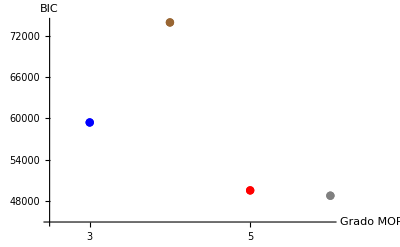

```mathematica
b =ListPlot[B,PlotStyle->{{Blue,Thin,PointSize[0.015]},{Brown,Thin,PointSize[0.015]},{Red,Thin,PointSize[0.015]},{Gray,Thin,PointSize[0.015]},{Purple,Thin,PointSize[0.015]}},AxesLabel->{"Grado MOP","BIC"},AxesOrigin->{2.5,45000},AxesStyle->Directive[Black, 12],Ticks->{{3,4,5,6,7,8}, Automatic},PlotRange->Full]
```

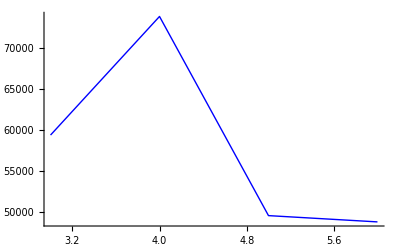

```mathematica
b1 =  ListLinePlot[B1,PlotStyle->{Blue,Thin}]
```

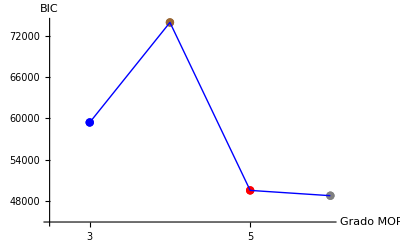

```mathematica
GrafBICChiMuestra1MA =Show[b,b1]
```

```mathematica
(*BIC con otra muestra*)
```

```mathematica
BIC3N = -2*L3 + 3*Log[10000]
```

59371.9

```mathematica
BIC4N = -2*L4 + 4*Log[10000]
```

73861.

```mathematica
BIC5N = -2*L5 + 5*Log[10000]
```

49538.1

```mathematica
BIC6N = -2*L6 + 6*Log[10000]
```

48759.7

```mathematica
BN={{{3,59371.947351155395}},{{4,73861.03675428589}},{{5,49538.08550642289}},{{6,48759.71256582492}}}
```

{{{3,59371.9}},{{4,73861.}},{{5,49538.1}},{{6,48759.7}}}

```mathematica
BN1 = {{3,59371.947351155395},{4,73861.03675428589},{5,49538.08550642289},{6,48759.71256582492}}
```

{{3,59371.9},{4,73861.},{5,49538.1},{6,48759.7}}

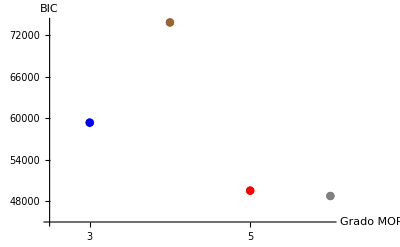

```mathematica
bN =ListPlot[BN,PlotStyle->{{Blue,Thin,PointSize[0.015]},{Brown,Thin,PointSize[0.015]},{Red,Thin,PointSize[0.015]},{Gray,Thin,PointSize[0.015]},{Purple,Thin,PointSize[0.015]}},AxesLabel->{"Grado MOP","BIC"},AxesOrigin->{2.5,45000},AxesStyle->Directive[Black, 12],Ticks->{{3,4,5,6,7,8}, Automatic},PlotRange->Full]
```

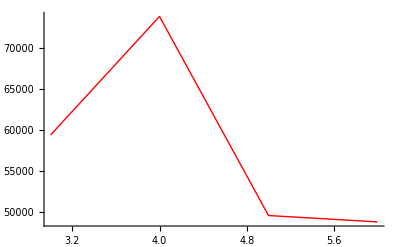

```mathematica
bN1 = ListLinePlot[BN1,PlotStyle->{Red,Thin}]
```

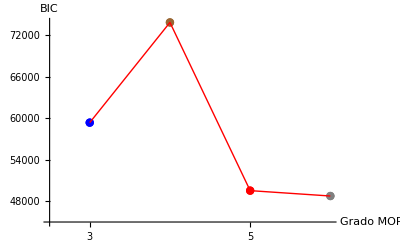

```mathematica
GrafBICChiMuestra2MA =Show[bN,bN1]
```

```mathematica
(*Comparación verosimilitudes con ambas muestras*)
```

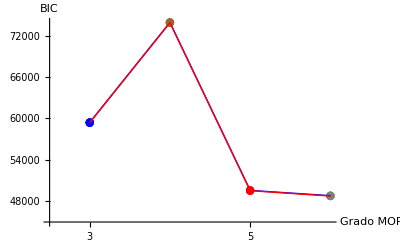

```mathematica
Show[GrafBICChiMuestra1MA,GrafBICChiMuestra2MA]
```

### MOMENTOS

```mathematica
Table[N[Integrate[x^i*PDF[ChiSquareDistribution[5],x],{x,0,Infinity}]],{i,1,8}]
```

{5.,35.,315.,3465.,45045.,675675.,1.14865×10^7,2.18243×10^8}

```mathematica
Muestrales=Table[(Apply[Plus,datos1^i])/10000,{i,1,8}]
```

{5.01025,35.3233,320.775,3541.44,45551.3,660392.,1.05128×10^7,1.79987×10^8}

```mathematica
f3estimada = Table[Integrate[x^i*f3[x],{x,0,25}],{i,1,8}]
```

{9.90928,127.854,1956.63,33749.,634484.,1.26969×10^7,2.65888×10^8,5.75599×10^9}

```mathematica
f4estimada = Table[Integrate[x^i*f4[x],{x,0,25}],{i,1,8}]
```

{13.4404,213.541,3741.38,69918.6,1.36775×10^6,2.7683×10^7,5.75224×10^8,1.22048×10^10}

```mathematica
f5estimada = Table[Integrate[x^i*f5[x],{x,0,25}],{i,1,8}]
```

{6.09571,56.1781,717.023,11550.2,214954.,4.34848×10^6,9.23685×10^7,2.02256×10^9}

```mathematica
f6estimada = Table[Integrate[x^i*f6[x],{x,0,25}],{i,1,8}]
```

{5.11062,36.6336,343.386,4114.23,61304.3,1.082×10^6,2.14108×10^7,4.54741×10^8}

```mathematica
f7estimada = Table[Integrate[x^i*f7[x],{x,0,25}],{i,1,8}]
```

{15.6038,258.715,4482.54,80410.1,1.48412×10^6,2.80571×10^7,5.41473×10^8,1.06404×10^10}

```mathematica
Table[{Integrate[x^i*f3[x],{x,0,25}],Integrate[x^i*f4[x],{x,0,25}],Integrate[x^i*f5[x],{x,0,25}],Integrate[x^i*f6[x],{x,0,25}],Integrate[x^i*f7[x],{x,0,25}]},{i,1,7}]
```

{{9.90928,13.4404,6.09571,5.11062,15.6038},{127.854,213.541,56.1781,36.6336,258.715},{1956.63,3741.38,717.023,343.386,4482.54},{33749.,69918.6,11550.2,4114.23,80410.1},{634484.,1.36775×10^6,214954.,61304.3,1.48412×10^6},{1.26969×10^7,2.7683×10^7,4.34848×10^6,1.082×10^6,2.80571×10^7},{2.65888×10^8,5.75224×10^8,9.23685×10^7,2.14108×10^7,5.41473×10^8}}